# Pivotal journal and other

## General rule

PMIDからISSNを引くルール：

```mathematica
Get["/Volumes/elecom/BANK/pubmed/202312/xml/element/journal/"<>"PMIDtoISSNrl.save"];
```

```mathematica
PMIDtoISSNrl["2"][[1]]
```

1090-2104

ISSNから雑誌タイトルを引くルール：

```mathematica
Get["/Volumes/elecom/BANK/pubmed/202312/xml/element/journal-title/ISSNvsTitle.save"];
```

```mathematica
ISSNvsTitle[PMIDtoISSNrl["2"][[1]]]
```

Biochemical and biophysical research communications

ジャーナルタイトルからIFを引くルール：

```mathematica
IFtbl=Import["/Volumes/elecom/BANK/pubmed/202312/exec_command/element/journal/clarivate/Journal Performance Data/最終集計.xlsx"];
```

```mathematica
IFtblHead=IFtbl[[1,1;;2]]
```

{{元ジャーナル名,Journal Title,ISSN,訂正ISSN,追加EISSN,最初刊行年,総論文数,1950.,1950.,1950.,1950.,1955.,1955.,1955.,1955.,1960.,1960.,1960.,1960.,1965.,1965.,1965.,1965.,1970.,1970.,1970.,1970.,1975.,1975.,1975.,1975.,1980.,1980.,1980.,1980.,,1985.,1985.,1985.,1985.,,1990.,1990.,1990.,1990.,,1995.,1995.,1995.,1995.,,2000.,2000.,2000.,2000.,,2005.,2005.,2005.,2005.,,2010.,2010.,2010.,2010.,,2015.,2015.,2015.,2015.,,2020.,2020.,2020.,2020.},{,,,,,,,JIF,過去2年間発表論文への被引用数,過去2年間の被引用対象論文数,総被引用回数,JIF,過去2年間発表論文への被引用数,過去2年間の被引用対象論文数,総被引用回数,JIF,過去2年間発表論文への被引用数,過去2年間の被引用対象論文数,総被引用回数,JIF,過去2年間発表論文への被引用数,過去2年間の被引用対象論文数,総被引用回数,JIF,過去2年間発表論文への被引用数,過去2年間の被引用対象論文数,総被引用回数,JIF,過去2年間発表論文への被引用数,過去2年間の被引用対象論文数,総被引用回数,JIF,過去2年間発表論文への被引用数,過去2年間の被引用対象論文数,総被引用回数,,JIF,過去2年間発表論文への被引用数,過去2年間の被引用対象論文数,総被引用回数,,JIF,過去2年間発表論文への被引用数,過去2年間の被引用対象論文数,総被引用回数,,JIF,過去2年間発表論文への被引用数,過去2年間の被引用対象論文数,総被引用回数,,JIF,過去2年間発表論文への被引用数,過去2年間の被引用対象論文数,総被引用回数,,JIF,過去2年間発表論文への被引用数,過去2年間の被引用対象論文数,総被引用回数,,JIF,過去2年間発表論文への被引用数,過去2年間の被引用対象論文数,総被引用回数,,JIF,過去2年間発表論文への被引用数,過去2年間の被引用対象論文数,総被引用回数,,JIF,過去2年間発表論文への被引用数,過去2年間の被引用対象論文数,総被引用回数}}

```mathematica
IFtblHead[[All,jifpos=Table[n,{n,52,72,5}]]]
```

{{2000.,2005.,2010.,2015.,2020.},{JIF,JIF,JIF,JIF,JIF}}

```mathematica
IFtblBody=IFtbl[[1,3;;]]
```

{{Annals of surgery,Annals of Surgery,0003-4932,,,1997.,7995（2020年まで）,,,,,,,,,,,,,,,,,,,,,,,,,,,,,,,,,,,,,,,,,,,,,5.987,2365.,395.,19555.,,6.328,2778.,439.,21713.,,7.474,3797.,508.,32990.,,8.569,5073.,592.,43775.,,12.969,8015.,604.,64045.},{Biochimica et biophysica acta,Biochimica et Biophysica Acta,0006-3002,,,1997.,3379（2020年まで）,,,,,,,,,,,,,,,,,,,,,,,,,,,,,,,,,,,,,,,,,,,,,,,,,,,,,,,,,,,,,,,,,,,,},{Bioinformatics (Oxford, England),Bioinformatics (Oxford, England),1367-4811,,,1998.,17319（2020年まで）,,,,,,,,,,,,,,,,,,,,,,,,,,,,,,,,,,,,,,,,,,,,,3.409,934.,246.,980.,,6.019,6037.,1003.,16784.,,4.877,6438.,1320.,40661.,,5.766,7957.,1380.,72448.,,6.937,12862.,1914.,149363.},{British medical journal,British Medical Journal,0007-1447,1756-1833,,1997.,8143(2012年まで）,,,,,,,,,,,,,,,,,,,,,,,,,,,,,,,,,,,,,,,,,,,,,5.331,8940.,1677.,51530.,,9.052,8545.,1248.,59516.,,13.471,8433.,626.,72217.,,,,,,,,,,},{Journal of bacteriology,Journal of Bacteriology,0021-9193,,,1997.,18,811(2020年まで）,,,,,,,,,,,,,,,,,,,,,,,,,,,,,,,,,,,,,,,,,,,,,3.506,7078.,2019.,46305.,,4.167,7688.,1845.,54861.,,3.726,6517.,1749.,62723.,,3.198,3124.,977.,65727.,,3.49,1930.,556.,69342.},{Journal of molecular biology,Journal of Molecular Biology,0022-2836,,,1997.,18,025(2020年まで),,,,,,,,,,,,,,,,,,,,,,,,,,,,,,,,,,,,,,,,,,,,,5.388,9914.,1840.,51848.,,5.229,9877.,1889.,63503.,,4.008,7896.,1970.,70522.,,4.517,2999.,664.,61523.,,5.469,3828.,700.,65163.},{Nature,Nature,0028-0836,,,1997.,26,896(2020年まで）,,,,,,,,,,,,,,,,,,,,,,,,,,,,,,,,,,,,,,,,,,,,,25.814,51525.,1996.,306184.,,29.273,50848.,1737.,372784.,,36.104,63724.,1765.,511248.,,38.138,65674.,1719.,627846.,,49.962,90281.,1807.,915939.},{PloS one,PLoS ONE,1932-6203,,,2009.,288,277(2020年まで),,,,,,,,,,,,,,,,,,,,,,,,,,,,,,,,,,,,,,,,,,,,,,,,,,,,,,,4.411,31404.,4263.,42795.,,3.057,188116.,61536.,425015.,,3.24,107508.,29123.,857751.},{Proceedings of the National Academy of Sciences of the United States of America,Proceedings of the National Academy of Sciences of the United States of America,0027-8424,,,1997.,90,098(2020年まで),,,,,,,,,,,,,,,,,,,,,,,,,,,,,,,,,,,,,,,,,,,,,10.789,57453.,5325.,302228.,,10.231,59429.,5809.,357239.,,9.771,71066.,7273.,482699.,,9.423,70581.,7480.,593284.,,11.205,74177.,6616.,799068.},{Proceedings of the Society for Experimental Biology and Medicine. Society for Experimental Biology and Medicine (New York, N.Y.),Proceedings of the Society for Experimental Biology and Medicine. Society for Experimental Biology and Medicine (New York, N.Y.),0037-9727,,,1997.,519(2002年まで),,,,,,,,,,,,,,,,,,,,,,,,,,,,,,,,,,,,,,,,,,,,,3.415,881.,258.,7196.,,,,,,,,,,,,,,,,,,,,},{The Biochemical journal,Biochemical journal,0264-6021,,,1997.,13367(2020年まで),,,,,,,,,,,,,,,,,,,,,,,,,,,,,,,,,,,,,,,,,,,,,4.28,7161.,1673.,49107.,,4.224,6455.,1528.,46855.,,5.016,4600.,917.,50717.,,3.562,2771.,778.,47760.,,3.857,1786.,455.,52813.},{The Journal of biological chemistry,Journal of biological chemistry,0021-9258,ISSN登録なし,1083-351X,1997.,101434(2020年まで),,,,,,,,,,,,,,,,,,,,,,,,,,,,,,,,,,,,,,,,,,,,,7.368,74361.,10093.,344256.,,5.854,76686.,13100.,404397.,,5.328,397747.,7447.,412004.,,4.258,26722.,6275.,377497.,,5.157,16218.,3145.,397474.},{The Journal of clinical investigation,Journal of clinical investigation,0021-9738,,,1997.,11290(2020年まで),,,,,,,,,,,,,,,,,,,,,,,,,,,,,,,,,,,,,,,,,,,,,12.015,11522.,959.,80103.,,15.053,10853.,721.,78425.,,14.152,9595.,678.,90822.,,12.575,11255.,897.,101063.,,14.808,11550.,788.,132303.},{The Journal of physiology,Journal of physiology,0022-3751,,,1997.,12911(2020年まで),,,,,,,,,,,,,,,,,,,,,,,,,,,,,,,,,,,,,,,,,,,,,4.455,5475.,1229.,40581.,,4.272,5280.,1236.,39568.,,5.139,4512.,878.,47530.,,4.731,3463.,732.,47457.,,5.182,3586.,674.,58036.}}

```mathematica
jtitle=Map[#[[1]]&,IFtblBody]
```

{Annals of surgery,Biochimica et biophysica acta,Bioinformatics (Oxford, England),British medical journal,Journal of bacteriology,Journal of molecular biology,Nature,PloS one,Proceedings of the National Academy of Sciences of the United States of America,Proceedings of the Society for Experimental Biology and Medicine. Society for Experimental Biology and Medicine (New York, N.Y.),The Biochemical journal,The Journal of biological chemistry,The Journal of clinical investigation,The Journal of physiology}

＜ジャーナルタイトルからIFを引くルール＞

```mathematica
jifyear={2000,2005,2010,2015,2020}
```

{2000,2005,2010,2015,2020}

```mathematica
jifatyear=Map[StringJoin,Map[ToString,Map[Map[Riffle[#,"/"]&,Inner[List,#,jifyear,List]]&,IFtblBody[[All,jifpos]]],{-1}]/.""->"-",{-2}]
```

{{5.987/2000,6.328/2005,7.474/2010,8.569/2015,12.969/2020},{-/2000,-/2005,-/2010,-/2015,-/2020},{3.409/2000,6.019/2005,4.877/2010,5.766/2015,6.937/2020},{5.331/2000,9.052/2005,13.471/2010,-/2015,-/2020},{3.506/2000,4.167/2005,3.726/2010,3.198/2015,3.49/2020},{5.388/2000,5.229/2005,4.008/2010,4.517/2015,5.469/2020},{25.814/2000,29.273/2005,36.104/2010,38.138/2015,49.962/2020},{-/2000,-/2005,4.411/2010,3.057/2015,3.24/2020},{10.789/2000,10.231/2005,9.771/2010,9.423/2015,11.205/2020},{3.415/2000,-/2005,-/2010,-/2015,-/2020},{4.28/2000,4.224/2005,5.016/2010,3.562/2015,3.857/2020},{7.368/2000,5.854/2005,5.328/2010,4.258/2015,5.157/2020},{12.015/2000,15.053/2005,14.152/2010,12.575/2015,14.808/2020},{4.455/2000,4.272/2005,5.139/2010,4.731/2015,5.182/2020}}

```mathematica
JTtoJIF=Association[Table[jtitle[[n]]->jifatyear[[n]],{n,1,Length[jtitle]}]]
```

<|Annals of surgery→{5.987/2000,6.328/2005,7.474/2010,8.569/2015,12.969/2020},Biochimica et biophysica acta→{-/2000,-/2005,-/2010,-/2015,-/2020},Bioinformatics (Oxford, England)→{3.409/2000,6.019/2005,4.877/2010,5.766/2015,6.937/2020},British medical journal→{5.331/2000,9.052/2005,13.471/2010,-/2015,-/2020},Journal of bacteriology→{3.506/2000,4.167/2005,3.726/2010,3.198/2015,3.49/2020},Journal of molecular biology→{5.388/2000,5.229/2005,4.008/2010,4.517/2015,5.469/2020},Nature→{25.814/2000,29.273/2005,36.104/2010,38.138/2015,49.962/2020},PloS one→{-/2000,-/2005,4.411/2010,3.057/2015,3.24/2020},Proceedings of the National Academy of Sciences of the United States of America→{10.789/2000,10.231/2005,9.771/2010,9.423/2015,11.205/2020},Proceedings of the Society for Experimental Biology and Medicine. Society for Experimental Biology and Medicine (New York, N.Y.)→{3.415/2000,-/2005,-/2010,-/2015,-/2020},The Biochemical journal→{4.28/2000,4.224/2005,5.016/2010,3.562/2015,3.857/2020},The Journal of biological chemistry→{7.368/2000,5.854/2005,5.328/2010,4.258/2015,5.157/2020},The Journal of clinical investigation→{12.015/2000,15.053/2005,14.152/2010,12.575/2015,14.808/2020},The Journal of physiology→{4.455/2000,4.272/2005,5.139/2010,4.731/2015,5.182/2020}|>

## All journal count

```mathematica
Get["/Volumes/elecom/BANK/pubmed/202312/xml/element/journal/ISSNvspubgenTly.save"];
```

```mathematica
(ISSNvspubgenTlyEf=Map[Cases[#,{{_},_}]&,ISSNvspubgenTly["All"]])//Length
```

15

```mathematica
totaljournalcount=Map[Length,ISSNvspubgenTlyEf]
```

{1800,2179,2713,4039,5279,7421,9874,11783,13747,15589,18276,20441,25956,31209,35252}

## G1: 主要雑誌(Q1)

## 別途必要なデータ

各累積世代の表示名

```mathematica
Get["/Volumes/elecom/BANK/pubmed/202312/exec_command/generations.wl"]
```

{1950,1955,1960,1965,1970,1975,1980,1985,1990,1995,2000,2005,2010,2015,2020}

各累積世代の主要論文数

```mathematica
top1PcCitedArtCount={10,30,46,50,38,33,32,26,19,22,33,66,192,315,336}
```

{10,30,46,50,38,33,32,26,19,22,33,66,192,315,336}

## Pivotal journal

```mathematica
Get["/Volumes/elecom/BANK/pubmed/202312/xml/element/journal/top1PcISSN.save"];
(* PMIDtoISSN.nbより *)
```

## 主要雑誌数累積

```mathematica
(top1pcISSN=Map[Flatten,Map[#[[1]]&,top1percISSNTallyBygenSort,{2}]])//Length
```

15

```mathematica
pivotaljournalcount=Map[Length,top1pcISSN]
```

{5,11,19,16,14,18,20,17,12,13,19,28,83,136,145}

## 新規出現主要雑誌累積

```mathematica
(top1pcISSNacm=Map[Flatten,FoldList[List,top1pcISSN]])//Length
```

15

```mathematica
(top1pcISSNnewcomer=Prepend[Table[Complement[top1pcISSNacm[[n+1]],top1pcISSNacm[[n]]],{n,1,14}],top1pcISSN[[1]]])//Length
```

15

```mathematica
top1pcISSNnewcomercount=Map[Length,top1pcISSNnewcomer]
```

{5,7,9,4,2,4,3,5,0,2,1,3,54,56,35}

## plot

```mathematica
ListPlot[{pivotaljournalcount,top1pcISSNnewcomercount},Joined->True,PlotRange->Full,Frame->True,FrameTicks->{Automatic,{genticks,None}},PlotLabels->{"主要雑誌数","新規出現主要雑誌数"}]
```

-Graphics-

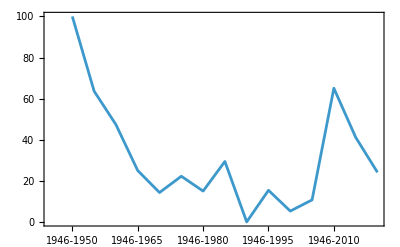

```mathematica
Labeled[ListPlot[top1pcISSNnewcomercount/pivotaljournalcount*100,Joined->True,
Frame->True,FrameTicks->{Automatic,{genticks,None}}],"新規出現雑誌の主要雑誌に占める割合（%）"]
```

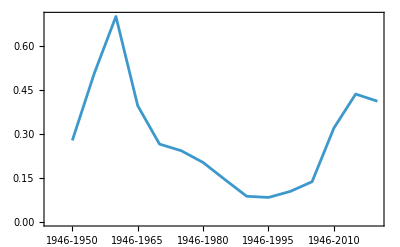

```mathematica
Labeled[ListPlot[pivotaljournalcount/totaljournalcount*100,Joined->True,Frame->True,FrameTicks->{Automatic,{genticks,None}}],"主要雑誌の全雑誌に占める割合（%）"]
```

## 主要雑誌タイトル

ISSN vs. journal title
ISSNvsTitle.save

< 主要雑誌ISSN一覧 >

```mathematica
pivotalJournalISSN=Cases[top1percISSNTallyBygenSort,_String,Infinity]//Union
```

{0001-6322,0001-690X,0002-8614,0002-9297,0002-9572,0003-2697,0003-2700,0003-276X,0003-4819,0003-4932,0003-9861,0003-990X,0004-3591,0005-3678,0006-291X,0006-2952,0006-2960,0006-341X,0006-3525,0007-0920,0007-1021,0007-9235,0009-9147,0010-4809,0012-0472,0012-186X,0014-2956,0014-4827,0016-6731,0018-4888,0019-2791,0020-5915,0021-8898,0021-9193,0021-9258,0021-9525,0021-9681,0021-9738,0022-1007,0022-1295,0022-1465,0022-1554,0022-1759,0022-1767,0022-2836,0022-2844,0022-3050,0022-3514,0022-3751,0022-3956,0022-5320,0025-7079,0027-8424,0027-8874,0028-0836,0028-3878,0028-3932,0028-4793,0031-6768,0031-6997,0032-0889,0033-2909,0033-8419,0036-8075,0042-6822,0066-4154,0076-6879,0077-8923,0085-591X,0090-3493,0092-8674,0095-1137,0095-9898,0095-9901,0096-9621,0098-7484,0099-2240,0108-7673,0140-6736,0146-0749,0147-006X,0149-5992,0160-6689,0161-8105,0162-3257,0163-1829,0165-0270,0165-1781,0168-8510,0168-9525,0169-1015,0173-0835,0192-8651,0195-9131,0197-2456,0261-4189,0263-7855,0264-6021,0266-7061,0270-7306,0271-6801,0277-6715,0305-1048,0366-0753,0366-0826,0378-1119,0512-3054,0586-7614,0737-4038,0740-3194,0749-503X,0884-8734,0888-7543,0903-1936,0907-4449,0925-2738,0950-1991,0952-0481,0959-8138,0960-7412,0962-1083,1046-2023,1049-7323,1053-8119,1058-8388,1061-4036,1063-5157,1064-3745,1065-9471,1076-836X,1079-5006,1079-7114,1088-9051,1095-9203,1096-987X,1097-0215,1097-4164,1097-4172,1098-5336,1176-9343,1353-4505,1362-4962,1367-4803,1367-4811,1399-0047,1465-3249,1465-4644,1465-7392,1467-5463,1471-003X,1471-0064,1471-2105,1471-2148,1471-2164,1474-1768,1474-547X,1474-760X,1476-4687,1520-6106,1523-6838,1524-4539,1524-4563,1530-0366,1530-8561,1532-0480,1533-4406,1537-1719,1538-3598,1539-3704,1542-4863,1544-6115,1546-1696,1546-1718,1548-7105,1549-1676,1549-5469,1554-351X,1557-7988,1557-8666,1558-5646,1558-8238,1660-8151,1744-4292,1750-2799,1756-1833,1879-0852,1937-9145,2046-4053,2053-2296,2159-8290}

```mathematica
(*Save["/Volumes/elecom/BANK/pubmed/202312/xml/element/journal/"<>"pivotalJournalISSNflatlist.save",pivotalJournalISSN]*)
```

pivotalJournalISSN　についてはJIFを取得する。

< 主要雑誌タイトルとそれに含まれる主要論文数 >

```mathematica
(topJournaltitleTbl=Map[{ISSNvsTitle[#[[1,1]]],#[[2]]}&,top1percISSNTallyBygenSort,{2}])//TableForm
```

Part::partw: {}の部分1は存在しません．

General::stop: この計算中に，Part::partwのこれ以上の出力は表示されません．

The Journal of clinical investigation
3 | The Biochemical journal
3 | Genetics
2 | Science (New York, N.Y.)
1 | American journal of public health and the nation's health
1 |  |  |  |  |  |  |  |  |  |  |  |  |  |  |  |  |  |  |  |  |  |  |  |  |  |  |  |  |  |  |  |  |  |  |  |  |  |  |  |  |  |  |  |  |  |  |  |  |  |  |  |  |  |  |  |  |  |  |  |  |  |  |  |  |  |  |  |  |  |  |  |  |  |  |  |  |  |  |  |  |  |  |  |  |  |  |  |  |  |  |  |  |  |  |  |  |  |  |  |  |  |  |  |  |  |  |  |  |  |  |  |  |  |  |  |  |  |  |  |  |  |  |  |  |  |  |  |  |  |  |  |  |  |  |  |  |  |  |  |  | 
The Biochemical journal
13 | The Journal of clinical investigation
5 | Science (New York, N.Y.)
2 | The Journal of physiology
2 | Genetics
2 | Biochemische Zeitschrift
1 | Journal of bacteriology
1 | The Journal of biological chemistry
1 | Deutsche medizinische Wochenschrift (1946)
1 | British journal of pharmacology and chemotherapy
1 | Nature
1 |  |  |  |  |  |  |  |  |  |  |  |  |  |  |  |  |  |  |  |  |  |  |  |  |  |  |  |  |  |  |  |  |  |  |  |  |  |  |  |  |  |  |  |  |  |  |  |  |  |  |  |  |  |  |  |  |  |  |  |  |  |  |  |  |  |  |  |  |  |  |  |  |  |  |  |  |  |  |  |  |  |  |  |  |  |  |  |  |  |  |  |  |  |  |  |  |  |  |  |  |  |  |  |  |  |  |  |  |  |  |  |  |  |  |  |  |  |  |  |  |  |  |  |  |  |  |  |  |  |  |  |  |  |  | 
The Biochemical journal
11 | The Journal of physiology
7 | The Journal of clinical investigation
4 | The Journal of experimental medicine
4 | The Journal of biological chemistry
3 | Science (New York, N.Y.)
2 | The Anatomical record
2 | The Journal of biophysical and biochemical cytology
2 | Journal of cellular and comparative physiology
1 | The journal of histochemistry and cytochemistry : official journal of the Histochemistry Society
1 | British journal of pharmacology and chemotherapy
1 | Archives of biochemistry
1 | The Journal of general physiology
1 | Lancet (London, England)
1 | Genetics
1 | Hoppe-Seyler's Zeitschrift fur physiologische Chemie
1 | Journal of bacteriology
1 | Deutsche medizinische Wochenschrift (1946)
1 | Nature
1 |  |  |  |  |  |  |  |  |  |  |  |  |  |  |  |  |  |  |  |  |  |  |  |  |  |  |  |  |  |  |  |  |  |  |  |  |  |  |  |  |  |  |  |  |  |  |  |  |  |  |  |  |  |  |  |  |  |  |  |  |  |  |  |  |  |  |  |  |  |  |  |  |  |  |  |  |  |  |  |  |  |  |  |  |  |  |  |  |  |  |  |  |  |  |  |  |  |  |  |  |  |  |  |  |  |  |  |  |  |  |  |  |  |  |  |  |  |  |  |  |  |  |  |  |  |  | 
The Biochemical journal
13 | The Journal of biophysical and biochemical cytology
8 | The Journal of biological chemistry
6 | The Journal of physiology
4 | The Journal of experimental medicine
4 | The Journal of cell biology
2 | Journal of bacteriology
2 | The Journal of clinical investigation
2 | Nature
2 | Hoppe-Seyler's Zeitschrift fur physiologische Chemie
1 | Archives of biochemistry
1 | Genetics
1 | Deutsche medizinische Wochenschrift (1946)
1 | British journal of experimental pathology
1 | International archives of allergy and applied immunology
1 | Journal of molecular biology
1 |  |  |  |  |  |  |  |  |  |  |  |  |  |  |  |  |  |  |  |  |  |  |  |  |  |  |  |  |  |  |  |  |  |  |  |  |  |  |  |  |  |  |  |  |  |  |  |  |  |  |  |  |  |  |  |  |  |  |  |  |  |  |  |  |  |  |  |  |  |  |  |  |  |  |  |  |  |  |  |  |  |  |  |  |  |  |  |  |  |  |  |  |  |  |  |  |  |  |  |  |  |  |  |  |  |  |  |  |  |  |  |  |  |  |  |  |  |  |  |  |  |  |  |  |  |  |  |  |  | 
The Biochemical journal
9 | The Journal of biophysical and biochemical cytology
6 | The Journal of experimental medicine
4 | The Journal of cell biology
4 | The Journal of biological chemistry
4 | The Journal of physiology
2 | Nature
2 | Annals of the New York Academy of Sciences
1 | The Journal of clinical investigation
1 | Science (New York, N.Y.)
1 | Journal of bacteriology
1 | Experimental cell research
1 | Journal of molecular biology
1 | International archives of allergy and applied immunology
1 |  |  |  |  |  |  |  |  |  |  |  |  |  |  |  |  |  |  |  |  |  |  |  |  |  |  |  |  |  |  |  |  |  |  |  |  |  |  |  |  |  |  |  |  |  |  |  |  |  |  |  |  |  |  |  |  |  |  |  |  |  |  |  |  |  |  |  |  |  |  |  |  |  |  |  |  |  |  |  |  |  |  |  |  |  |  |  |  |  |  |  |  |  |  |  |  |  |  |  |  |  |  |  |  |  |  |  |  |  |  |  |  |  |  |  |  |  |  |  |  |  |  |  |  |  |  |  |  |  |  |  | 
The Journal of biological chemistry
7 | The Journal of cell biology
4 | The Biochemical journal
3 | The Journal of biophysical and biochemical cytology
3 | Nature
2 | The Journal of experimental medicine
2 | Journal of immunology (Baltimore, Md. : 1950)
1 | The Journal of clinical investigation
1 | Plant physiology
1 | Virology
1 | The Journal of physiology
1 | Journal of molecular biology
1 | Experimental cell research
1 | Journal of bacteriology
1 | Science (New York, N.Y.)
1 | Immunochemistry
1 | International archives of allergy and applied immunology
1 | Annals of the New York Academy of Sciences
1 |  |  |  |  |  |  |  |  |  |  |  |  |  |  |  |  |  |  |  |  |  |  |  |  |  |  |  |  |  |  |  |  |  |  |  |  |  |  |  |  |  |  |  |  |  |  |  |  |  |  |  |  |  |  |  |  |  |  |  |  |  |  |  |  |  |  |  |  |  |  |  |  |  |  |  |  |  |  |  |  |  |  |  |  |  |  |  |  |  |  |  |  |  |  |  |  |  |  |  |  |  |  |  |  |  |  |  |  |  |  |  |  |  |  |  |  |  |  |  |  |  |  |  |  |  |  |  | 
The Journal of biological chemistry
7 | The Journal of cell biology
3 | The Journal of experimental medicine
2 | The Biochemical journal
2 | The Journal of biophysical and biochemical cytology
2 | Experimental cell research
1 | European journal of biochemistry
1 | Journal of molecular biology
1 | Bacteriological reviews
1 | Virology
1 | Missing[KeyAbsent,{{},1}⟦1,1⟧]
1 | Journal of ultrastructure research
1 | Plant physiology
1 | The Journal of physiology
1 | Science (New York, N.Y.)
1 | Journal of bacteriology
1 | The journal of histochemistry and cytochemistry : official journal of the Histochemistry Society
1 | International archives of allergy and applied immunology
1 | Immunochemistry
1 | Annals of the New York Academy of Sciences
1 | Nature
1 |  |  |  |  |  |  |  |  |  |  |  |  |  |  |  |  |  |  |  |  |  |  |  |  |  |  |  |  |  |  |  |  |  |  |  |  |  |  |  |  |  |  |  |  |  |  |  |  |  |  |  |  |  |  |  |  |  |  |  |  |  |  |  |  |  |  |  |  |  |  |  |  |  |  |  |  |  |  |  |  |  |  |  |  |  |  |  |  |  |  |  |  |  |  |  |  |  |  |  |  |  |  |  |  |  |  |  |  |  |  |  |  |  |  |  |  |  |  |  |  |  |  |  |  | 
The Journal of biological chemistry
5 | Proceedings of the National Academy of Sciences of the United States of America
4 | Journal of molecular biology
2 | Biochemistry
1 | Journal of ultrastructure research
1 | Missing[KeyAbsent,{{},1}⟦1,1⟧]
1 | The journal of histochemistry and cytochemistry : official journal of the Histochemistry Society
1 | Plant physiology
1 | Nucleic acids research
1 | Immunochemistry
1 | European journal of biochemistry
1 | Annals of the New York Academy of Sciences
1 | The Biochemical journal
1 | Analytical biochemistry
1 | Methods in enzymology
1 | The Journal of biophysical and biochemical cytology
1 | The Journal of cell biology
1 | Nature
1 |  |  |  |  |  |  |  |  |  |  |  |  |  |  |  |  |  |  |  |  |  |  |  |  |  |  |  |  |  |  |  |  |  |  |  |  |  |  |  |  |  |  |  |  |  |  |  |  |  |  |  |  |  |  |  |  |  |  |  |  |  |  |  |  |  |  |  |  |  |  |  |  |  |  |  |  |  |  |  |  |  |  |  |  |  |  |  |  |  |  |  |  |  |  |  |  |  |  |  |  |  |  |  |  |  |  |  |  |  |  |  |  |  |  |  |  |  |  |  |  |  |  |  |  |  |  |  | 
The Journal of biological chemistry
4 | Proceedings of the National Academy of Sciences of the United States of America
3 | Analytical biochemistry
2 | Journal of molecular biology
2 | Annals of the New York Academy of Sciences
1 | The Biochemical journal
1 | The Journal of biophysical and biochemical cytology
1 | Biochemistry
1 | Nucleic acids research
1 | The Journal of cell biology
1 | Methods in enzymology
1 | Nature
1 |  |  |  |  |  |  |  |  |  |  |  |  |  |  |  |  |  |  |  |  |  |  |  |  |  |  |  |  |  |  |  |  |  |  |  |  |  |  |  |  |  |  |  |  |  |  |  |  |  |  |  |  |  |  |  |  |  |  |  |  |  |  |  |  |  |  |  |  |  |  |  |  |  |  |  |  |  |  |  |  |  |  |  |  |  |  |  |  |  |  |  |  |  |  |  |  |  |  |  |  |  |  |  |  |  |  |  |  |  |  |  |  |  |  |  |  |  |  |  |  |  |  |  |  |  |  |  |  |  |  |  |  |  | 
The Journal of biological chemistry
4 | Analytical biochemistry
3 | Proceedings of the National Academy of Sciences of the United States of America
3 | Nucleic acids research
2 | Journal of molecular biology
2 | The Journal of biophysical and biochemical cytology
1 | Pflugers Archiv : European journal of physiology
1 | Science (New York, N.Y.)
1 | Gene
1 | The Journal of cell biology
1 | Biochemistry
1 | Methods in enzymology
1 | Nature
1 |  |  |  |  |  |  |  |  |  |  |  |  |  |  |  |  |  |  |  |  |  |  |  |  |  |  |  |  |  |  |  |  |  |  |  |  |  |  |  |  |  |  |  |  |  |  |  |  |  |  |  |  |  |  |  |  |  |  |  |  |  |  |  |  |  |  |  |  |  |  |  |  |  |  |  |  |  |  |  |  |  |  |  |  |  |  |  |  |  |  |  |  |  |  |  |  |  |  |  |  |  |  |  |  |  |  |  |  |  |  |  |  |  |  |  |  |  |  |  |  |  |  |  |  |  |  |  |  |  |  |  |  | 
Journal of molecular biology
4 | Proceedings of the National Academy of Sciences of the United States of America
4 | The Journal of biological chemistry
4 | Nucleic acids research
3 | Analytical biochemistry
3 | Journal of bacteriology
1 | European journal of biochemistry
1 | Annals of the New York Academy of Sciences
1 | The Biochemical journal
1 | The Journal of biophysical and biochemical cytology
1 | Virology
1 | Missing[KeyAbsent,{{},1}⟦1,1⟧]
1 | Molecular and cellular biology
1 | Science (New York, N.Y.)
1 | Pflugers Archiv : European journal of physiology
1 | The Journal of cell biology
1 | Gene
1 | Biochemistry
1 | Methods in enzymology
1 | Nature
1 |  |  |  |  |  |  |  |  |  |  |  |  |  |  |  |  |  |  |  |  |  |  |  |  |  |  |  |  |  |  |  |  |  |  |  |  |  |  |  |  |  |  |  |  |  |  |  |  |  |  |  |  |  |  |  |  |  |  |  |  |  |  |  |  |  |  |  |  |  |  |  |  |  |  |  |  |  |  |  |  |  |  |  |  |  |  |  |  |  |  |  |  |  |  |  |  |  |  |  |  |  |  |  |  |  |  |  |  |  |  |  |  |  |  |  |  |  |  |  |  |  |  |  |  |  | 
Proceedings of the National Academy of Sciences of the United States of America
8 | Nucleic acids research
6 | Journal of molecular biology
6 | Analytical biochemistry
6 | The Journal of biological chemistry
6 | Gene
4 | Methods in enzymology
4 | The journal of histochemistry and cytochemistry : official journal of the Histochemistry Society
2 | Journal of bacteriology
2 | Science (New York, N.Y.)
2 | Nature
2 | Acta crystallographica. Section A, Foundations of crystallography
1 | Journal of ultrastructure research
1 | Scandinavian journal of clinical and laboratory investigation. Supplementum
1 | The Journal of physiology
1 | Immunochemistry
1 | Plant physiology
1 | European journal of biochemistry
1 | Genetics
1 | Molecular biology and evolution
1 | The Biochemical journal
1 | Annals of the New York Academy of Sciences
1 | The Journal of biophysical and biochemical cytology
1 | Virology
1 | Molecular and cellular biology
1 | Missing[KeyAbsent,{{},1}⟦1,1⟧]
1 | Pflugers Archiv : European journal of physiology
1 | The Journal of cell biology
1 | Biochemistry
1 |  |  |  |  |  |  |  |  |  |  |  |  |  |  |  |  |  |  |  |  |  |  |  |  |  |  |  |  |  |  |  |  |  |  |  |  |  |  |  |  |  |  |  |  |  |  |  |  |  |  |  |  |  |  |  |  |  |  |  |  |  |  |  |  |  |  |  |  |  |  |  |  |  |  |  |  |  |  |  |  |  |  |  |  |  |  |  |  |  |  |  |  |  |  |  |  |  |  |  |  |  |  |  |  |  |  |  |  |  |  |  |  |  |  |  |  | 
Proceedings of the National Academy of Sciences of the United States of America
14 | Nature
14 | Journal of molecular biology
11 | Nucleic acids research
10 | Analytical biochemistry
9 | Gene
8 | The Journal of biological chemistry
8 | Science (New York, N.Y.)
6 | Cell
5 | Methods in enzymology
5 | Bioinformatics (Oxford, England)
4 | Acta crystallographica. Section D, Biological crystallography
4 | CA: a cancer journal for clinicians
3 | Nucleic acids research
3 | Nature
2 | Computer applications in the biosciences : CABIOS
2 | The New England journal of medicine
2 | Journal of molecular graphics
2 | JAMA
2 | The EMBO journal
2 | The journal of histochemistry and cytochemistry : official journal of the Histochemistry Society
2 | Arthritis and rheumatism
2 | European journal of biochemistry
2 | The Biochemical journal
2 | Lancet (London, England)
2 | Journal of bacteriology
2 | Molecular and cellular biology
2 | Genetics
2 | Molecular biology and evolution
2 | The Journal of cell biology
2 | Biochemistry
2 | Acta crystallographica. Section A, Foundations of crystallography
2 | Microbiological reviews
1 | Biostatistics (Oxford, England)
1 | Journal of the National Cancer Institute
1 | Genome research
1 | JAMA
1 | Yeast (Chichester, England)
1 | Journal of chronic diseases
1 | Acta psychiatrica Scandinavica
1 | Archives of biochemistry and biophysics
1 | Journal of molecular and applied genetics
1 | Genome biology
1 | Annual review of biochemistry
1 | Biochemical and biophysical research communications
1 | Systematic biology
1 | Journal of clinical microbiology
1 | Genomics
1 | Development (Cambridge, England)
1 | Biochemical pharmacology
1 | Diabetologia
1 | Electrophoresis
1 | Journal of neurology, neurosurgery, and psychiatry
1 | Journal of personality and social psychology
1 | Archives of general psychiatry
1 | Journal of molecular evolution
1 | Pharmacological reviews
1 | Biopolymers
1 | Clinical chemistry
1 | Biometrics
1 | Methods in molecular biology (Clifton, N.J.)
1 | Journal of ultrastructure research
1 | Journal of biomolecular NMR
1 | Evolution; international journal of organic evolution
1 | Neuropsychologia
1 | Scandinavian journal of clinical and laboratory investigation. Supplementum
1 | Immunochemistry
1 | Neurology
1 | Briefings in bioinformatics
1 | The Plant journal : for cell and molecular biology
1 | Plant physiology
1 | Medical care
1 | The Journal of physiology
1 | Acta crystallographica. Section D, Biological crystallography
1 | Journal of immunological methods
1 | Annals of the New York Academy of Sciences
1 | The Journal of biophysical and biochemical cytology
1 | Nature genetics
1 | Virology
1 | Missing[KeyAbsent,{{},1}⟦1,1⟧]
1 | Journal of psychiatric research
1 | Methods (San Diego, Calif.)
1 | Methods in enzymology
1 | Pflugers Archiv : European journal of physiology
1 |  |  |  |  |  |  |  |  |  |  |  |  |  |  |  |  |  |  |  |  |  |  |  |  |  |  |  |  |  |  |  |  |  |  |  |  |  |  |  |  |  |  |  |  |  |  |  |  |  |  |  |  |  |  |  |  |  |  |  |  |  | 
Nature
20 | Proceedings of the National Academy of Sciences of the United States of America
16 | Cell
11 | Journal of molecular biology
11 | Nucleic acids research
11 | Nature
9 | Science (New York, N.Y.)
9 | Analytical biochemistry
8 | Genome research
7 | The Journal of biological chemistry
7 | The New England journal of medicine
6 | Bioinformatics (Oxford, England)
6 | Acta crystallographica. Section D, Biological crystallography
6 | Genome biology
5 | Bioinformatics (Oxford, England)
5 | Nucleic acids research
5 | CA: a cancer journal for clinicians
5 | Nature methods
4 | Genetics
4 | CA: a cancer journal for clinicians
4 | Gene
4 | Methods in enzymology
4 | Acta crystallographica. Section D, Biological crystallography
4 | Science (New York, N.Y.)
3 | JAMA
3 | Cell
3 | Nature genetics
3 | Molecular biology and evolution
3 | Psychological bulletin
2 | Biochemical pharmacology
2 | Acta neuropathologica
2 | NeuroImage
2 | Journal of bacteriology
2 | The New England journal of medicine
2 | Archives of general psychiatry
2 | Journal of the National Cancer Institute
2 | Journal of personality and social psychology
2 | Arthritis and rheumatism
2 | Journal of computational chemistry
2 | Journal of molecular graphics
2 | Medical care
2 | BMJ (Clinical research ed.)
2 | Biometrics
2 | Controlled clinical trials
2 | Nature protocols
2 | Lancet (London, England)
2 | Molecular biology and evolution
2 | Acta crystallographica. Section A, Foundations of crystallography
2 | British journal of cancer
1 | Genomics
1 | Magnetic resonance in medicine
1 | Nature reviews. Neuroscience
1 | European journal of cancer (Oxford, England : 1990)
1 | Analytical chemistry
1 | Annual review of biochemistry
1 | Developmental dynamics : an official publication of the American Association of Anatomists
1 | Genome research
1 | Applied and environmental microbiology
1 | Journal of health and social behavior
1 | Annual review of neuroscience
1 | Journal of autism and developmental disorders
1 | Health policy (Amsterdam, Netherlands)
1 | Radiology
1 | Nature reviews. Genetics
1 | Journal of clinical microbiology
1 | Pharmacological reviews
1 | Trends in genetics : TIG
1 | Yeast (Chichester, England)
1 | Evolutionary bioinformatics online
1 | Journal of ultrastructure research
1 | Nature biotechnology
1 | Schizophrenia bulletin
1 | Psychiatry research
1 | BMC genomics
1 | Physical review. B, Condensed matter
1 | Immunochemistry
1 | Computer applications in the biosciences : CABIOS
1 | British journal of addiction
1 | Nephron
1 | Journal of general internal medicine
1 | American journal of kidney diseases : the official journal of the National Kidney Foundation
1 | Scandinavian journal of clinical and laboratory investigation. Supplementum
1 | Archives of biochemistry and biophysics
1 | The journal of histochemistry and cytochemistry : official journal of the Histochemistry Society
1 | Critical care medicine
1 | BMC evolutionary biology
1 | Diabetes care
1 | Hypertension (Dallas, Tex. : 1979)
1 | Computers and biomedical research, an international journal
1 | JAMA
1 | The Journal of clinical psychiatry
1 | The journal of physical chemistry. B
1 | Electrophoresis
1 | Annals of internal medicine
1 | Development (Cambridge, England)
1 | European journal of biochemistry
1 | Spatial vision
1 | World Health Organization technical report series
1 | The Biochemical journal
1 | Biopolymers
1 | Plant physiology
1 | Circulation
1 | The EMBO journal
1 | The Journal of biophysical and biochemical cytology
1 | Annals of the New York Academy of Sciences
1 | Briefings in bioinformatics
1 | Journal of molecular evolution
1 | Statistics in medicine
1 | Molecular and cellular biology
1 | The Journal of physiology
1 | Virology
1 | International journal of cancer
1 | Biostatistics (Oxford, England)
1 | Journal of neurology, neurosurgery, and psychiatry
1 | Acta psychiatrica Scandinavica
1 | Systematic biology
1 | Statistical applications in genetics and molecular biology
1 | Clinical chemistry
1 | Journal of biomolecular NMR
1 | Evolution; international journal of organic evolution
1 | Journal of applied crystallography
1 | Methods in molecular biology (Clifton, N.J.)
1 | Neurology
1 | Diabetologia
1 | The Plant journal : for cell and molecular biology
1 | Journal of immunological methods
1 | Journal of chronic diseases
1 | BMJ (Clinical research ed.)
1 | The Journal of cell biology
1 | Neuropsychologia
1 | Biochemistry
1 | Pflugers Archiv : European journal of physiology
1 | American journal of human genetics
1 | Missing[KeyAbsent,{{},1}⟦1,1⟧]
1 | Methods in enzymology
1 | Journal of psychiatric research
1 | Methods (San Diego, Calif.)
1 |  |  |  |  |  |  |  |  | 
Bioinformatics (Oxford, England)
17 | CA: a cancer journal for clinicians
13 | Nature
12 | Proceedings of the National Academy of Sciences of the United States of America
10 | Nucleic acids research
10 | The New England journal of medicine
9 | Cell
9 | Genome biology
8 | Nucleic acids research
8 | Journal of molecular biology
8 | Nature
8 | Nature methods
7 | Bioinformatics (Oxford, England)
6 | Acta crystallographica. Section D, Biological crystallography
6 | Science (New York, N.Y.)
5 | Genome research
5 | Analytical biochemistry
5 | The Journal of biological chemistry
5 | NeuroImage
4 | Science (New York, N.Y.)
4 | Nature biotechnology
4 | Genetics
4 | Lancet (London, England)
4 | Molecular biology and evolution
4 | Acta crystallographica. Section D, Biological crystallography
4 | Cell
4 | BMC bioinformatics
3 | JAMA
3 | CA: a cancer journal for clinicians
3 | JAMA
3 | Biometrics
3 | Molecular biology and evolution
3 | BMJ (Clinical research ed.)
3 | Nature protocols
3 | Acta neuropathologica
2 | Circulation
2 | The New England journal of medicine
2 | Applied and environmental microbiology
2 | Systematic biology
2 | Psychological bulletin
2 | Journal of the National Cancer Institute
2 | Archives of general psychiatry
2 | Annals of internal medicine
2 | Journal of personality and social psychology
2 | Medical care
2 | International journal of cancer
2 | Lancet (London, England)
2 | Controlled clinical trials
2 | Journal of computational chemistry
2 | Nature genetics
2 | Acta crystallographica. Section A, Foundations of crystallography
2 | Acta crystallographica. Section C, Structural chemistry
1 | Developmental dynamics : an official publication of the American Association of Anatomists
1 | Sleep
1 | Virology
1 | Systematic reviews
1 | Molecular cell
1 | International journal for quality in health care : journal of the International Society for Quality in Health Care
1 | The EMBO journal
1 | Hypertension (Dallas, Tex. : 1979)
1 | American journal of kidney diseases : the official journal of the National Kidney Foundation
1 | Magnetic resonance in medicine
1 | Radiology
1 | Archives of biochemistry and biophysics
1 | Trends in genetics : TIG
1 | Development (Cambridge, England)
1 | Plant physiology
1 | BMC evolutionary biology
1 | Diabetes care
1 | Human brain mapping
1 | Nature reviews. Cancer
1 | The Journal of clinical investigation
1 | Critical care medicine
1 | Journal of the American Geriatrics Society
1 | Journal of computational chemistry
1 | British journal of addiction
1 | The journal of physical chemistry. B
1 | Biopolymers
1 | The European respiratory journal
1 | Clinical chemistry
1 | Nature cell biology
1 | Medicine and science in sports and exercise
1 | Nature reviews. Genetics
1 | The Journal of physiology
1 | Annals of internal medicine
1 | Schizophrenia bulletin
1 | Health policy (Amsterdam, Netherlands)
1 | Computers and biomedical research, an international journal
1 | The journals of gerontology. Series A, Biological sciences and medical sciences
1 | Journal of neuroscience methods
1 | Nature genetics
1 | Genetics in medicine : official journal of the American College of Medical Genetics
1 | Science signaling
1 | Qualitative health research
1 | Molecular ecology
1 | Molecular systems biology
1 | Physical review. B, Condensed matter
1 | Cytotherapy
1 | Cancer discovery
1 | Journal of molecular evolution
1 | Journal of health and social behavior
1 | BMC genomics
1 | Biostatistics (Oxford, England)
1 | Systematic biology
1 | World Health Organization technical report series
1 | Methods in molecular biology (Clifton, N.J.)
1 | Spatial vision
1 | Arthritis and rheumatism
1 | The Journal of clinical psychiatry
1 | Psychiatry research
1 | Statistical applications in genetics and molecular biology
1 | Applied and environmental microbiology
1 | Annals of surgery
1 | Biochemistry
1 | Journal of biomolecular NMR
1 | Journal of neurology, neurosurgery, and psychiatry
1 | Physical review letters
1 | The Journal of cell biology
1 | Pflugers Archiv : European journal of physiology
1 | Journal of computational biology : a journal of computational molecular cell biology
1 | Clinical chemistry
1 | Behavior research methods
1 | Evolution; international journal of organic evolution
1 | Methods in enzymology
1 | Gene
1 | Neurology
1 | Journal of general internal medicine
1 | European journal of cancer (Oxford, England : 1990)
1 | Statistics in medicine
1 | Journal of biomedical informatics
1 | Genome research
1 | The Plant journal : for cell and molecular biology
1 | Diabetologia
1 | Journal of immunological methods
1 | Acta psychiatrica Scandinavica
1 | Missing[KeyAbsent,{{},1}⟦1,1⟧]
1 | Journal of applied crystallography
1 | Neuropsychologia
1 | Journal of molecular graphics
1 | PLoS medicine
1 | Journal of chronic diseases
1 | American journal of human genetics
1 | Methods in enzymology
1 | BMJ (Clinical research ed.)
1 | Journal of psychiatric research
1 | Methods (San Diego, Calif.)
1

```mathematica
topJournaltitleTbl//Length
```

15

< topoftopJournal >

```mathematica
(topoftopJournaltitle={topJournaltitleTbl[[1]][[1;;2]],
topJournaltitleTbl[[2]][[1;;1]],
topJournaltitleTbl[[3]][[1;;1]],
topJournaltitleTbl[[4]][[1;;1]],
topJournaltitleTbl[[5]][[1;;1]],
topJournaltitleTbl[[6]][[1;;1]],
topJournaltitleTbl[[7]][[1;;1]],
topJournaltitleTbl[[8]][[1;;1]],
topJournaltitleTbl[[9]][[1;;1]],
topJournaltitleTbl[[10]][[1;;1]],
topJournaltitleTbl[[11]][[1;;2]],
topJournaltitleTbl[[12]][[1;;1]],
topJournaltitleTbl[[13]][[1;;2]],
topJournaltitleTbl[[14]][[1;;1]],
topJournaltitleTbl[[15]][[1;;1]]
})//TableForm
```

The Journal of clinical investigation
3 | The Biochemical journal
3
The Biochemical journal
13 | 
The Biochemical journal
11 | 
The Biochemical journal
13 | 
The Biochemical journal
9 | 
The Journal of biological chemistry
7 | 
The Journal of biological chemistry
7 | 
The Journal of biological chemistry
5 | 
The Journal of biological chemistry
4 | 
The Journal of biological chemistry
4 | 
Journal of molecular biology
4 | Proceedings of the National Academy of Sciences of the United States of America
4
Proceedings of the National Academy of Sciences of the United States of America
8 | 
Proceedings of the National Academy of Sciences of the United States of America
14 | Nature
14
Nature
20 | 
Bioinformatics (Oxford, England)
17 |

カウントだけ抜き出す

```mathematica
topoftopJournaltitleCount=Map[#[[1]][[2]]&,topoftopJournaltitle]
```

{3,13,11,13,9,7,7,5,4,4,4,8,14,20,17}

< 当該誌の主要論文が当該世代主要論文に占める割合(%) >

```mathematica
topoftopJournaltitleCountRatio=topoftopJournaltitleCount/top1PcCitedArtCount*100//N//Round
```

{30,43,24,26,24,21,22,19,21,18,12,12,7,6,5}

< topoftopISSN >

```mathematica
(topoftopISSNlist={top1pcISSN[[1]][[1;;2]],
top1pcISSN[[2]][[1;;1]],
top1pcISSN[[3]][[1;;1]],
top1pcISSN[[4]][[1;;1]],
top1pcISSN[[5]][[1;;1]],
top1pcISSN[[6]][[1;;1]],
top1pcISSN[[7]][[1;;1]],
top1pcISSN[[8]][[1;;1]],
top1pcISSN[[9]][[1;;1]],
top1pcISSN[[10]][[1;;1]],
top1pcISSN[[11]][[1;;2]],
top1pcISSN[[12]][[1;;1]],
top1pcISSN[[13]][[1;;2]],
top1pcISSN[[14]][[1;;1]],
top1pcISSN[[15]][[1;;1]]
})//TableForm
```

0021-9738 | 0264-6021
0264-6021 | 
0264-6021 | 
0264-6021 | 
0264-6021 | 
0021-9258 | 
0021-9258 | 
0021-9258 | 
0021-9258 | 
0021-9258 | 
0022-2836 | 0027-8424
0027-8424 | 
0027-8424 | 0028-0836
0028-0836 | 
1367-4811 |

インパクトファクター(IF)とその発表年についてはJCRから求めた。

```mathematica
topoftopJIF=Map[JTtoJIF[#[[1]]]&,topoftopJournaltitle,{-2}]
```

{{{12.015/2000,15.053/2005,14.152/2010,12.575/2015,14.808/2020},{4.28/2000,4.224/2005,5.016/2010,3.562/2015,3.857/2020}},{{4.28/2000,4.224/2005,5.016/2010,3.562/2015,3.857/2020}},{{4.28/2000,4.224/2005,5.016/2010,3.562/2015,3.857/2020}},{{4.28/2000,4.224/2005,5.016/2010,3.562/2015,3.857/2020}},{{4.28/2000,4.224/2005,5.016/2010,3.562/2015,3.857/2020}},{{7.368/2000,5.854/2005,5.328/2010,4.258/2015,5.157/2020}},{{7.368/2000,5.854/2005,5.328/2010,4.258/2015,5.157/2020}},{{7.368/2000,5.854/2005,5.328/2010,4.258/2015,5.157/2020}},{{7.368/2000,5.854/2005,5.328/2010,4.258/2015,5.157/2020}},{{7.368/2000,5.854/2005,5.328/2010,4.258/2015,5.157/2020}},{{5.388/2000,5.229/2005,4.008/2010,4.517/2015,5.469/2020},{10.789/2000,10.231/2005,9.771/2010,9.423/2015,11.205/2020}},{{10.789/2000,10.231/2005,9.771/2010,9.423/2015,11.205/2020}},{{10.789/2000,10.231/2005,9.771/2010,9.423/2015,11.205/2020},{25.814/2000,29.273/2005,36.104/2010,38.138/2015,49.962/2020}},{{25.814/2000,29.273/2005,36.104/2010,38.138/2015,49.962/2020}},{{3.409/2000,6.019/2005,4.877/2010,5.766/2015,6.937/2020}}}

```mathematica
(pivotalJournaltblbody=Transpose[{gen,topoftopJournaltitle,topoftopJournaltitleCountRatio,pivotaljournalcount,topoftopJIF}])//TableForm
```

1946-1950 | The Journal of clinical investigation | 3
The Biochemical journal | 3 | 30 | 5 | 12.015/2000 | 15.053/2005 | 14.152/2010 | 12.575/2015 | 14.808/2020
4.28/2000 | 4.224/2005 | 5.016/2010 | 3.562/2015 | 3.857/2020
1946-1955 | The Biochemical journal | 13 | 43 | 11 | 4.28/2000 | 4.224/2005 | 5.016/2010 | 3.562/2015 | 3.857/2020
1946-1960 | The Biochemical journal | 11 | 24 | 19 | 4.28/2000 | 4.224/2005 | 5.016/2010 | 3.562/2015 | 3.857/2020
1946-1965 | The Biochemical journal | 13 | 26 | 16 | 4.28/2000 | 4.224/2005 | 5.016/2010 | 3.562/2015 | 3.857/2020
1946-1970 | The Biochemical journal | 9 | 24 | 14 | 4.28/2000 | 4.224/2005 | 5.016/2010 | 3.562/2015 | 3.857/2020
1946-1975 | The Journal of biological chemistry | 7 | 21 | 18 | 7.368/2000 | 5.854/2005 | 5.328/2010 | 4.258/2015 | 5.157/2020
1946-1980 | The Journal of biological chemistry | 7 | 22 | 20 | 7.368/2000 | 5.854/2005 | 5.328/2010 | 4.258/2015 | 5.157/2020
1946-1985 | The Journal of biological chemistry | 5 | 19 | 17 | 7.368/2000 | 5.854/2005 | 5.328/2010 | 4.258/2015 | 5.157/2020
1946-1990 | The Journal of biological chemistry | 4 | 21 | 12 | 7.368/2000 | 5.854/2005 | 5.328/2010 | 4.258/2015 | 5.157/2020
1946-1995 | The Journal of biological chemistry | 4 | 18 | 13 | 7.368/2000 | 5.854/2005 | 5.328/2010 | 4.258/2015 | 5.157/2020
1946-2000 | Journal of molecular biology | 4
Proceedings of the National Academy of Sciences of the United States of America | 4 | 12 | 19 | 5.388/2000 | 5.229/2005 | 4.008/2010 | 4.517/2015 | 5.469/2020
10.789/2000 | 10.231/2005 | 9.771/2010 | 9.423/2015 | 11.205/2020
1946-2005 | Proceedings of the National Academy of Sciences of the United States of America | 8 | 12 | 28 | 10.789/2000 | 10.231/2005 | 9.771/2010 | 9.423/2015 | 11.205/2020
1946-2010 | Proceedings of the National Academy of Sciences of the United States of America | 14
Nature | 14 | 7 | 83 | 10.789/2000 | 10.231/2005 | 9.771/2010 | 9.423/2015 | 11.205/2020
25.814/2000 | 29.273/2005 | 36.104/2010 | 38.138/2015 | 49.962/2020
1946-2015 | Nature | 20 | 6 | 136 | 25.814/2000 | 29.273/2005 | 36.104/2010 | 38.138/2015 | 49.962/2020
1946-2020 | Bioinformatics (Oxford, England) | 17 | 5 | 145 | 3.409/2000 | 6.019/2005 | 4.877/2010 | 5.766/2015 | 6.937/2020

```mathematica
pivotalJournaltblhead={"累積世代",{{"雑誌タイトル","当該誌の\n高被引用論文数"}},{{"当該誌の高被引用論文が\n当該累積世代の高被引用論文\n全体に占める割合(%)"}},{"当該累積世代の\n主要雑誌数"},{{"IF","/IF発表年"}}}
```

{累積世代,{{雑誌タイトル,当該誌の
高被引用論文数}},{{当該誌の高被引用論文が
当該累積世代の高被引用論文
全体に占める割合(%)}},{当該累積世代の
主要雑誌数},{{IF,/IF発表年}}}

```mathematica
Prepend[pivotalJournaltblbody,pivotalJournaltblhead]//TableForm
```

累積世代 | 雑誌タイトル | 当該誌の
高被引用論文数 | 当該誌の高被引用論文が
当該累積世代の高被引用論文
全体に占める割合(%) | 当該累積世代の
主要雑誌数 | IF | /IF発表年
1946-1950 | The Journal of clinical investigation | 3
The Biochemical journal | 3 | 30 | 5 | 12.015/2000 | 15.053/2005 | 14.152/2010 | 12.575/2015 | 14.808/2020
4.28/2000 | 4.224/2005 | 5.016/2010 | 3.562/2015 | 3.857/2020
1946-1955 | The Biochemical journal | 13 | 43 | 11 | 4.28/2000 | 4.224/2005 | 5.016/2010 | 3.562/2015 | 3.857/2020
1946-1960 | The Biochemical journal | 11 | 24 | 19 | 4.28/2000 | 4.224/2005 | 5.016/2010 | 3.562/2015 | 3.857/2020
1946-1965 | The Biochemical journal | 13 | 26 | 16 | 4.28/2000 | 4.224/2005 | 5.016/2010 | 3.562/2015 | 3.857/2020
1946-1970 | The Biochemical journal | 9 | 24 | 14 | 4.28/2000 | 4.224/2005 | 5.016/2010 | 3.562/2015 | 3.857/2020
1946-1975 | The Journal of biological chemistry | 7 | 21 | 18 | 7.368/2000 | 5.854/2005 | 5.328/2010 | 4.258/2015 | 5.157/2020
1946-1980 | The Journal of biological chemistry | 7 | 22 | 20 | 7.368/2000 | 5.854/2005 | 5.328/2010 | 4.258/2015 | 5.157/2020
1946-1985 | The Journal of biological chemistry | 5 | 19 | 17 | 7.368/2000 | 5.854/2005 | 5.328/2010 | 4.258/2015 | 5.157/2020
1946-1990 | The Journal of biological chemistry | 4 | 21 | 12 | 7.368/2000 | 5.854/2005 | 5.328/2010 | 4.258/2015 | 5.157/2020
1946-1995 | The Journal of biological chemistry | 4 | 18 | 13 | 7.368/2000 | 5.854/2005 | 5.328/2010 | 4.258/2015 | 5.157/2020
1946-2000 | Journal of molecular biology | 4
Proceedings of the National Academy of Sciences of the United States of America | 4 | 12 | 19 | 5.388/2000 | 5.229/2005 | 4.008/2010 | 4.517/2015 | 5.469/2020
10.789/2000 | 10.231/2005 | 9.771/2010 | 9.423/2015 | 11.205/2020
1946-2005 | Proceedings of the National Academy of Sciences of the United States of America | 8 | 12 | 28 | 10.789/2000 | 10.231/2005 | 9.771/2010 | 9.423/2015 | 11.205/2020
1946-2010 | Proceedings of the National Academy of Sciences of the United States of America | 14
Nature | 14 | 7 | 83 | 10.789/2000 | 10.231/2005 | 9.771/2010 | 9.423/2015 | 11.205/2020
25.814/2000 | 29.273/2005 | 36.104/2010 | 38.138/2015 | 49.962/2020
1946-2015 | Nature | 20 | 6 | 136 | 25.814/2000 | 29.273/2005 | 36.104/2010 | 38.138/2015 | 49.962/2020
1946-2020 | Bioinformatics (Oxford, England) | 17 | 5 | 145 | 3.409/2000 | 6.019/2005 | 4.877/2010 | 5.766/2015 | 6.937/2020

< 主要雑誌数含む >

```mathematica
(G1JournalTbl=Map[{#[[1]],#[[2,All,1]],#[[2,All,2]],#[[3]],#[[4]],#[[5]]}&,Prepend[pivotalJournaltblbody,pivotalJournaltblhead]])//TableForm
```

累積世代 | 雑誌タイトル | 当該誌の
高被引用論文数 | 当該誌の高被引用論文が
当該累積世代の高被引用論文
全体に占める割合(%) | 当該累積世代の
主要雑誌数 | IF | /IF発表年
1946-1950 | The Journal of clinical investigation
The Biochemical journal | 3
3 | 30 | 5 | 12.015/2000 | 15.053/2005 | 14.152/2010 | 12.575/2015 | 14.808/2020
4.28/2000 | 4.224/2005 | 5.016/2010 | 3.562/2015 | 3.857/2020
1946-1955 | The Biochemical journal | 13 | 43 | 11 | 4.28/2000 | 4.224/2005 | 5.016/2010 | 3.562/2015 | 3.857/2020
1946-1960 | The Biochemical journal | 11 | 24 | 19 | 4.28/2000 | 4.224/2005 | 5.016/2010 | 3.562/2015 | 3.857/2020
1946-1965 | The Biochemical journal | 13 | 26 | 16 | 4.28/2000 | 4.224/2005 | 5.016/2010 | 3.562/2015 | 3.857/2020
1946-1970 | The Biochemical journal | 9 | 24 | 14 | 4.28/2000 | 4.224/2005 | 5.016/2010 | 3.562/2015 | 3.857/2020
1946-1975 | The Journal of biological chemistry | 7 | 21 | 18 | 7.368/2000 | 5.854/2005 | 5.328/2010 | 4.258/2015 | 5.157/2020
1946-1980 | The Journal of biological chemistry | 7 | 22 | 20 | 7.368/2000 | 5.854/2005 | 5.328/2010 | 4.258/2015 | 5.157/2020
1946-1985 | The Journal of biological chemistry | 5 | 19 | 17 | 7.368/2000 | 5.854/2005 | 5.328/2010 | 4.258/2015 | 5.157/2020
1946-1990 | The Journal of biological chemistry | 4 | 21 | 12 | 7.368/2000 | 5.854/2005 | 5.328/2010 | 4.258/2015 | 5.157/2020
1946-1995 | The Journal of biological chemistry | 4 | 18 | 13 | 7.368/2000 | 5.854/2005 | 5.328/2010 | 4.258/2015 | 5.157/2020
1946-2000 | Journal of molecular biology
Proceedings of the National Academy of Sciences of the United States of America | 4
4 | 12 | 19 | 5.388/2000 | 5.229/2005 | 4.008/2010 | 4.517/2015 | 5.469/2020
10.789/2000 | 10.231/2005 | 9.771/2010 | 9.423/2015 | 11.205/2020
1946-2005 | Proceedings of the National Academy of Sciences of the United States of America | 8 | 12 | 28 | 10.789/2000 | 10.231/2005 | 9.771/2010 | 9.423/2015 | 11.205/2020
1946-2010 | Proceedings of the National Academy of Sciences of the United States of America
Nature | 14
14 | 7 | 83 | 10.789/2000 | 10.231/2005 | 9.771/2010 | 9.423/2015 | 11.205/2020
25.814/2000 | 29.273/2005 | 36.104/2010 | 38.138/2015 | 49.962/2020
1946-2015 | Nature | 20 | 6 | 136 | 25.814/2000 | 29.273/2005 | 36.104/2010 | 38.138/2015 | 49.962/2020
1946-2020 | Bioinformatics (Oxford, England) | 17 | 5 | 145 | 3.409/2000 | 6.019/2005 | 4.877/2010 | 5.766/2015 | 6.937/2020

< 最終形式 >

```mathematica
(finalG1JournalTbl=G1JournalTbl[[All,{1,2,3,4,6}]])//TableForm
```

累積世代 | 雑誌タイトル | 当該誌の
高被引用論文数 | 当該誌の高被引用論文が
当該累積世代の高被引用論文
全体に占める割合(%) | IF | /IF発表年
1946-1950 | The Journal of clinical investigation
The Biochemical journal | 3
3 | 30 | 12.015/2000 | 15.053/2005 | 14.152/2010 | 12.575/2015 | 14.808/2020
4.28/2000 | 4.224/2005 | 5.016/2010 | 3.562/2015 | 3.857/2020
1946-1955 | The Biochemical journal | 13 | 43 | 4.28/2000 | 4.224/2005 | 5.016/2010 | 3.562/2015 | 3.857/2020
1946-1960 | The Biochemical journal | 11 | 24 | 4.28/2000 | 4.224/2005 | 5.016/2010 | 3.562/2015 | 3.857/2020
1946-1965 | The Biochemical journal | 13 | 26 | 4.28/2000 | 4.224/2005 | 5.016/2010 | 3.562/2015 | 3.857/2020
1946-1970 | The Biochemical journal | 9 | 24 | 4.28/2000 | 4.224/2005 | 5.016/2010 | 3.562/2015 | 3.857/2020
1946-1975 | The Journal of biological chemistry | 7 | 21 | 7.368/2000 | 5.854/2005 | 5.328/2010 | 4.258/2015 | 5.157/2020
1946-1980 | The Journal of biological chemistry | 7 | 22 | 7.368/2000 | 5.854/2005 | 5.328/2010 | 4.258/2015 | 5.157/2020
1946-1985 | The Journal of biological chemistry | 5 | 19 | 7.368/2000 | 5.854/2005 | 5.328/2010 | 4.258/2015 | 5.157/2020
1946-1990 | The Journal of biological chemistry | 4 | 21 | 7.368/2000 | 5.854/2005 | 5.328/2010 | 4.258/2015 | 5.157/2020
1946-1995 | The Journal of biological chemistry | 4 | 18 | 7.368/2000 | 5.854/2005 | 5.328/2010 | 4.258/2015 | 5.157/2020
1946-2000 | Journal of molecular biology
Proceedings of the National Academy of Sciences of the United States of America | 4
4 | 12 | 5.388/2000 | 5.229/2005 | 4.008/2010 | 4.517/2015 | 5.469/2020
10.789/2000 | 10.231/2005 | 9.771/2010 | 9.423/2015 | 11.205/2020
1946-2005 | Proceedings of the National Academy of Sciences of the United States of America | 8 | 12 | 10.789/2000 | 10.231/2005 | 9.771/2010 | 9.423/2015 | 11.205/2020
1946-2010 | Proceedings of the National Academy of Sciences of the United States of America
Nature | 14
14 | 7 | 10.789/2000 | 10.231/2005 | 9.771/2010 | 9.423/2015 | 11.205/2020
25.814/2000 | 29.273/2005 | 36.104/2010 | 38.138/2015 | 49.962/2020
1946-2015 | Nature | 20 | 6 | 25.814/2000 | 29.273/2005 | 36.104/2010 | 38.138/2015 | 49.962/2020
1946-2020 | Bioinformatics (Oxford, England) | 17 | 5 | 3.409/2000 | 6.019/2005 | 4.877/2010 | 5.766/2015 | 6.937/2020

## G2: Q2雑誌

## Q2論文(とそれを引用する論文)

変数: topCitingCitedArt26Perc[YYYY, "citing rule"]

```mathematica
Q2mainartfiles=Table["/Volumes/elecom/BANK/pubmed/202312/xml/element/reference/1946-"<>ToString[n]<>"_topCitingCitedArt26Perc.save",{n,1950,2020,5}]
```

{/Volumes/elecom/BANK/pubmed/202312/xml/element/reference/1946-1950_topCitingCitedArt26Perc.save,/Volumes/elecom/BANK/pubmed/202312/xml/element/reference/1946-1955_topCitingCitedArt26Perc.save,/Volumes/elecom/BANK/pubmed/202312/xml/element/reference/1946-1960_topCitingCitedArt26Perc.save,/Volumes/elecom/BANK/pubmed/202312/xml/element/reference/1946-1965_topCitingCitedArt26Perc.save,/Volumes/elecom/BANK/pubmed/202312/xml/element/reference/1946-1970_topCitingCitedArt26Perc.save,/Volumes/elecom/BANK/pubmed/202312/xml/element/reference/1946-1975_topCitingCitedArt26Perc.save,/Volumes/elecom/BANK/pubmed/202312/xml/element/reference/1946-1980_topCitingCitedArt26Perc.save,/Volumes/elecom/BANK/pubmed/202312/xml/element/reference/1946-1985_topCitingCitedArt26Perc.save,/Volumes/elecom/BANK/pubmed/202312/xml/element/reference/1946-1990_topCitingCitedArt26Perc.save,/Volumes/elecom/BANK/pubmed/202312/xml/element/reference/1946-1995_topCitingCitedArt26Perc.save,/Volumes/elecom/BANK/pubmed/202312/xml/element/reference/1946-2000_topCitingCitedArt26Perc.save,/Volumes/elecom/BANK/pubmed/202312/xml/element/reference/1946-2005_topCitingCitedArt26Perc.save,/Volumes/elecom/BANK/pubmed/202312/xml/element/reference/1946-2010_topCitingCitedArt26Perc.save,/Volumes/elecom/BANK/pubmed/202312/xml/element/reference/1946-2015_topCitingCitedArt26Perc.save,/Volumes/elecom/BANK/pubmed/202312/xml/element/reference/1946-2020_topCitingCitedArt26Perc.save}

```mathematica
Map[Get,Q2mainartfiles];
```

## Q2 journal

cited論文（Q2論文）だけにする

```mathematica
Q2PMID["year"]=Table[Map[#[[1,2]]&,topCitingCitedArt26Perc[n,"citing rule"]],{n,1950,2020,5}]
```

```mathematica
(Q2PMID["unique"]=Union[Flatten[Q2PMID["year"]]])//Length
```

89021

ISSN:

```mathematica
(Q2ISSN["year"]=Map[PMIDtoISSNrl,Q2PMID["year"],{2}])//Length
```

15

```mathematica
(Q2ISSN["year","tally"]=Map[Reverse[SortBy[Tally[Flatten[#]],Last]]&,Q2ISSN["year"]])//Length
```

15

Journal name:

```mathematica
Q2Jtitle=Map[{ISSNvsTitle[#[[1]]],#[[2]]}&,Q2ISSN["year","tally"],{2}];
```

:代表（メジャー） Journal name:

:タイの確認:

```mathematica
Map[#[[1]]==#[[2]]&,Q2Jtitle]
```

{False,False,False,False,False,False,False,False,False,False,False,False,False,False,False}

世代におけるメジャー誌:

```mathematica
Q2MajourJTitle=Map[{ISSNvsTitle[#],#}&,Map[#[[1,1]]&,Q2ISSN["year","tally"]]]
```

{{Journal of bacteriology,0021-9193},{The Biochemical journal,0264-6021},{The Biochemical journal,0264-6021},{The Biochemical journal,0264-6021},{The Journal of biological chemistry,0021-9258},{The Journal of physiology,0022-3751},{The Journal of biological chemistry,0021-9258},{Proceedings of the National Academy of Sciences of the United States of America,0027-8424},{Proceedings of the National Academy of Sciences of the United States of America,0027-8424},{Proceedings of the National Academy of Sciences of the United States of America,0027-8424},{Proceedings of the National Academy of Sciences of the United States of America,0027-8424},{Proceedings of the National Academy of Sciences of the United States of America,0027-8424},{Proceedings of the National Academy of Sciences of the United States of America,0027-8424},{Proceedings of the National Academy of Sciences of the United States of America,0027-8424},{Proceedings of the National Academy of Sciences of the United States of America,0027-8424}}

＜メジャー誌と論文カウント＞

```mathematica
Q2MajourJCount=Map[#[[1]]&,Q2Jtitle]
```

{{Journal of bacteriology,34},{The Biochemical journal,20},{The Biochemical journal,64},{The Biochemical journal,62},{The Journal of biological chemistry,90},{The Journal of physiology,98},{The Journal of biological chemistry,150},{Proceedings of the National Academy of Sciences of the United States of America,214},{Proceedings of the National Academy of Sciences of the United States of America,316},{Proceedings of the National Academy of Sciences of the United States of America,410},{Proceedings of the National Academy of Sciences of the United States of America,490},{Proceedings of the National Academy of Sciences of the United States of America,715},{Proceedings of the National Academy of Sciences of the United States of America,947},{Proceedings of the National Academy of Sciences of the United States of America,882},{Proceedings of the National Academy of Sciences of the United States of America,810}}

＜グループ論文カウント・率＞

```mathematica
Q2ArtCount=Map[Total,Map[#[[2]]&,Q2ISSN["year","tally"],{2}]]
```

{76,303,615,931,1434,2039,2807,3647,4646,5911,7225,9756,14634,19426,25213}

```mathematica
Q2MajourJRatio=Round[Map[#[[2]]&,Q2MajourJCount]/Q2ArtCount*100//N]
```

{45,7,10,7,6,5,5,6,7,7,7,7,6,5,3}

＜IF＞

```mathematica
Q2JIF=Map[StringJoin[Riffle[JTtoJIF[#[[1,1]]]," "]]&,Q2Jtitle]
```

{3.506/2000 4.167/2005 3.726/2010 3.198/2015 3.49/2020,4.28/2000 4.224/2005 5.016/2010 3.562/2015 3.857/2020,4.28/2000 4.224/2005 5.016/2010 3.562/2015 3.857/2020,4.28/2000 4.224/2005 5.016/2010 3.562/2015 3.857/2020,7.368/2000 5.854/2005 5.328/2010 4.258/2015 5.157/2020,4.455/2000 4.272/2005 5.139/2010 4.731/2015 5.182/2020,7.368/2000 5.854/2005 5.328/2010 4.258/2015 5.157/2020,10.789/2000 10.231/2005 9.771/2010 9.423/2015 11.205/2020,10.789/2000 10.231/2005 9.771/2010 9.423/2015 11.205/2020,10.789/2000 10.231/2005 9.771/2010 9.423/2015 11.205/2020,10.789/2000 10.231/2005 9.771/2010 9.423/2015 11.205/2020,10.789/2000 10.231/2005 9.771/2010 9.423/2015 11.205/2020,10.789/2000 10.231/2005 9.771/2010 9.423/2015 11.205/2020,10.789/2000 10.231/2005 9.771/2010 9.423/2015 11.205/2020,10.789/2000 10.231/2005 9.771/2010 9.423/2015 11.205/2020}

＜項目名＞

```mathematica
Q2Journaltblhead={"累積世代","雑誌タイトル","当該誌の\nG2論文数","当該誌のG2論文が\n当該累積世代のG2論文\n全体に占める割合(%)","IF / 発表年"}
```

{累積世代,雑誌タイトル,当該誌の
G2論文数,当該誌のG2論文が
当該累積世代のG2論文
全体に占める割合(%),IF / 発表年}

＜＜表＞＞

```mathematica
Prepend[{gen,Map[#[[1]]&,Q2MajourJCount],Map[#[[2]]&,Q2MajourJCount],Q2MajourJRatio,Q2JIF}//Transpose,Q2Journaltblhead]//TableForm
```

累積世代 | 雑誌タイトル | 当該誌の
G2論文数 | 当該誌のG2論文が
当該累積世代のG2論文
全体に占める割合(%) | IF / 発表年
1946-1950 | Journal of bacteriology | 34 | 45 | 3.506/2000 4.167/2005 3.726/2010 3.198/2015 3.49/2020
1946-1955 | The Biochemical journal | 20 | 7 | 4.28/2000 4.224/2005 5.016/2010 3.562/2015 3.857/2020
1946-1960 | The Biochemical journal | 64 | 10 | 4.28/2000 4.224/2005 5.016/2010 3.562/2015 3.857/2020
1946-1965 | The Biochemical journal | 62 | 7 | 4.28/2000 4.224/2005 5.016/2010 3.562/2015 3.857/2020
1946-1970 | The Journal of biological chemistry | 90 | 6 | 7.368/2000 5.854/2005 5.328/2010 4.258/2015 5.157/2020
1946-1975 | The Journal of physiology | 98 | 5 | 4.455/2000 4.272/2005 5.139/2010 4.731/2015 5.182/2020
1946-1980 | The Journal of biological chemistry | 150 | 5 | 7.368/2000 5.854/2005 5.328/2010 4.258/2015 5.157/2020
1946-1985 | Proceedings of the National Academy of Sciences of the United States of America | 214 | 6 | 10.789/2000 10.231/2005 9.771/2010 9.423/2015 11.205/2020
1946-1990 | Proceedings of the National Academy of Sciences of the United States of America | 316 | 7 | 10.789/2000 10.231/2005 9.771/2010 9.423/2015 11.205/2020
1946-1995 | Proceedings of the National Academy of Sciences of the United States of America | 410 | 7 | 10.789/2000 10.231/2005 9.771/2010 9.423/2015 11.205/2020
1946-2000 | Proceedings of the National Academy of Sciences of the United States of America | 490 | 7 | 10.789/2000 10.231/2005 9.771/2010 9.423/2015 11.205/2020
1946-2005 | Proceedings of the National Academy of Sciences of the United States of America | 715 | 7 | 10.789/2000 10.231/2005 9.771/2010 9.423/2015 11.205/2020
1946-2010 | Proceedings of the National Academy of Sciences of the United States of America | 947 | 6 | 10.789/2000 10.231/2005 9.771/2010 9.423/2015 11.205/2020
1946-2015 | Proceedings of the National Academy of Sciences of the United States of America | 882 | 5 | 10.789/2000 10.231/2005 9.771/2010 9.423/2015 11.205/2020
1946-2020 | Proceedings of the National Academy of Sciences of the United States of America | 810 | 3 | 10.789/2000 10.231/2005 9.771/2010 9.423/2015 11.205/2020

全累積世代の出現雑誌（ユニーク）：

```mathematica
(Q2ISSN["total"]=Union[Flatten[Q2ISSN["year"]]])//Length
```

4560

## G3: Q3雑誌

## Q3論文(とそれを引用する論文)

変数: topCitingCitedArt51Perc[YYYY, "citing rule"]

```mathematica
Q3mainartfiles=Table["/Volumes/elecom/BANK/pubmed/202312/xml/element/reference/1946-"<>ToString[n]<>"_topCitingCitedArt51Perc.save",{n,1950,2020,5}]
```

{/Volumes/elecom/BANK/pubmed/202312/xml/element/reference/1946-1950_topCitingCitedArt51Perc.save,/Volumes/elecom/BANK/pubmed/202312/xml/element/reference/1946-1955_topCitingCitedArt51Perc.save,/Volumes/elecom/BANK/pubmed/202312/xml/element/reference/1946-1960_topCitingCitedArt51Perc.save,/Volumes/elecom/BANK/pubmed/202312/xml/element/reference/1946-1965_topCitingCitedArt51Perc.save,/Volumes/elecom/BANK/pubmed/202312/xml/element/reference/1946-1970_topCitingCitedArt51Perc.save,/Volumes/elecom/BANK/pubmed/202312/xml/element/reference/1946-1975_topCitingCitedArt51Perc.save,/Volumes/elecom/BANK/pubmed/202312/xml/element/reference/1946-1980_topCitingCitedArt51Perc.save,/Volumes/elecom/BANK/pubmed/202312/xml/element/reference/1946-1985_topCitingCitedArt51Perc.save,/Volumes/elecom/BANK/pubmed/202312/xml/element/reference/1946-1990_topCitingCitedArt51Perc.save,/Volumes/elecom/BANK/pubmed/202312/xml/element/reference/1946-1995_topCitingCitedArt51Perc.save,/Volumes/elecom/BANK/pubmed/202312/xml/element/reference/1946-2000_topCitingCitedArt51Perc.save,/Volumes/elecom/BANK/pubmed/202312/xml/element/reference/1946-2005_topCitingCitedArt51Perc.save,/Volumes/elecom/BANK/pubmed/202312/xml/element/reference/1946-2010_topCitingCitedArt51Perc.save,/Volumes/elecom/BANK/pubmed/202312/xml/element/reference/1946-2015_topCitingCitedArt51Perc.save,/Volumes/elecom/BANK/pubmed/202312/xml/element/reference/1946-2020_topCitingCitedArt51Perc.save}

```mathematica
Map[Get,Q3mainartfiles];
```

## Q3 journal

cited論文（Q3論文）だけにする

```mathematica
Q3PMID["year"]=Table[Map[#[[1,2]]&,topCitingCitedArt51Perc[n,"citing rule"]],{n,1950,2020,5}]
```

```mathematica
(Q3PMID["unique"]=Union[Flatten[Q3PMID["year"]]])//Length
```

248228

ISSN:

```mathematica
(Q3ISSN["year"]=Map[PMIDtoISSNrl,Q3PMID["year"],{2}])//Length
```

15

```mathematica
(Q3ISSN["year","tally"]=Map[Reverse[SortBy[Tally[Flatten[#]],Last]]&,Q3ISSN["year"]])//Length
```

15

Journal name:

```mathematica
Q3Jtitle=Map[{ISSNvsTitle[#[[1]]],#[[2]]}&,Q3ISSN["year","tally"],{2}];
```

:代表（メジャー） Journal name:

:タイの確認:

```mathematica
Map[#[[1]]==#[[2]]&,Q3Jtitle]
```

{False,False,False,False,False,False,False,False,False,False,False,False,False,False,False}

世代におけるメジャー誌:

```mathematica
Q3MajourJTitle=Map[{ISSNvsTitle[#],#}&,Map[#[[1,1]]&,Q3ISSN["year","tally"]]]
```

{{The Biochemical journal,0264-6021},{The Journal of biological chemistry,0021-9258},{Proceedings of the Society for Experimental Biology and Medicine. Society for Experimental Biology and Medicine (New York, N.Y.),0037-9727},{The Journal of biological chemistry,0021-9258},{The Journal of biological chemistry,0021-9258},{The Journal of biological chemistry,0021-9258},{The Biochemical journal,0264-6021},{Proceedings of the National Academy of Sciences of the United States of America,0027-8424},{The Journal of biological chemistry,0021-9258},{The Journal of biological chemistry,0021-9258},{The Journal of biological chemistry,0021-9258},{The Journal of biological chemistry,0021-9258},{The Journal of biological chemistry,0021-9258},{The Journal of biological chemistry,0021-9258},{The Journal of biological chemistry,0021-9258}}

＜メジャー誌と論文カウント＞

```mathematica
Q3MajourJCount=Map[#[[1]]&,Q3Jtitle]
```

{{The Biochemical journal,41},{The Journal of biological chemistry,21},{Proceedings of the Society for Experimental Biology and Medicine. Society for Experimental Biology and Medicine (New York, N.Y.),71},{The Journal of biological chemistry,72},{The Journal of biological chemistry,116},{The Journal of biological chemistry,205},{The Biochemical journal,267},{Proceedings of the National Academy of Sciences of the United States of America,388},{The Journal of biological chemistry,440},{The Journal of biological chemistry,782},{The Journal of biological chemistry,897},{The Journal of biological chemistry,1419},{The Journal of biological chemistry,1681},{The Journal of biological chemistry,1976},{The Journal of biological chemistry,1678}}

＜グループ論文カウント・率＞

```mathematica
Q3ArtCount=Map[Total,Map[#[[2]]&,Q3ISSN["year","tally"],{2}]]
```

{168,593,1541,2237,3407,5086,6918,8777,11853,15910,19674,26058,38327,53038,71672}

```mathematica
Q3MajourJRatio=Round[Map[#[[2]]&,Q3MajourJCount]/Q3ArtCount*100//N]
```

{24,4,5,3,3,4,4,4,4,5,5,5,4,4,2}

＜IF＞

```mathematica
Q3JIF=Map[StringJoin[Riffle[JTtoJIF[#[[1,1]]]," "]]&,Q3Jtitle]
```

{4.28/2000 4.224/2005 5.016/2010 3.562/2015 3.857/2020,7.368/2000 5.854/2005 5.328/2010 4.258/2015 5.157/2020,3.415/2000 -/2005 -/2010 -/2015 -/2020,7.368/2000 5.854/2005 5.328/2010 4.258/2015 5.157/2020,7.368/2000 5.854/2005 5.328/2010 4.258/2015 5.157/2020,7.368/2000 5.854/2005 5.328/2010 4.258/2015 5.157/2020,4.28/2000 4.224/2005 5.016/2010 3.562/2015 3.857/2020,10.789/2000 10.231/2005 9.771/2010 9.423/2015 11.205/2020,7.368/2000 5.854/2005 5.328/2010 4.258/2015 5.157/2020,7.368/2000 5.854/2005 5.328/2010 4.258/2015 5.157/2020,7.368/2000 5.854/2005 5.328/2010 4.258/2015 5.157/2020,7.368/2000 5.854/2005 5.328/2010 4.258/2015 5.157/2020,7.368/2000 5.854/2005 5.328/2010 4.258/2015 5.157/2020,7.368/2000 5.854/2005 5.328/2010 4.258/2015 5.157/2020,7.368/2000 5.854/2005 5.328/2010 4.258/2015 5.157/2020}

＜項目名＞

```mathematica
Q3Journaltblhead={"累積世代","雑誌タイトル","当該誌の\nG3論文数","当該誌のG3論文が\n当該累積世代のG3論文\n全体に占める割合(%)","IF / 発表年"}
```

{累積世代,雑誌タイトル,当該誌の
G3論文数,当該誌のG3論文が
当該累積世代のG3論文
全体に占める割合(%),IF / 発表年}

＜＜表＞＞

```mathematica
Prepend[{gen,Map[#[[1]]&,Q3MajourJCount],Map[#[[2]]&,Q3MajourJCount],Q3MajourJRatio,Q3JIF}//Transpose,Q3Journaltblhead]//TableForm
```

累積世代 | 雑誌タイトル | 当該誌の
G3論文数 | 当該誌のG3論文が
当該累積世代のG3論文
全体に占める割合(%) | IF / 発表年
1946-1950 | The Biochemical journal | 41 | 24 | 4.28/2000 4.224/2005 5.016/2010 3.562/2015 3.857/2020
1946-1955 | The Journal of biological chemistry | 21 | 4 | 7.368/2000 5.854/2005 5.328/2010 4.258/2015 5.157/2020
1946-1960 | Proceedings of the Society for Experimental Biology and Medicine. Society for Experimental Biology and Medicine (New York, N.Y.) | 71 | 5 | 3.415/2000 -/2005 -/2010 -/2015 -/2020
1946-1965 | The Journal of biological chemistry | 72 | 3 | 7.368/2000 5.854/2005 5.328/2010 4.258/2015 5.157/2020
1946-1970 | The Journal of biological chemistry | 116 | 3 | 7.368/2000 5.854/2005 5.328/2010 4.258/2015 5.157/2020
1946-1975 | The Journal of biological chemistry | 205 | 4 | 7.368/2000 5.854/2005 5.328/2010 4.258/2015 5.157/2020
1946-1980 | The Biochemical journal | 267 | 4 | 4.28/2000 4.224/2005 5.016/2010 3.562/2015 3.857/2020
1946-1985 | Proceedings of the National Academy of Sciences of the United States of America | 388 | 4 | 10.789/2000 10.231/2005 9.771/2010 9.423/2015 11.205/2020
1946-1990 | The Journal of biological chemistry | 440 | 4 | 7.368/2000 5.854/2005 5.328/2010 4.258/2015 5.157/2020
1946-1995 | The Journal of biological chemistry | 782 | 5 | 7.368/2000 5.854/2005 5.328/2010 4.258/2015 5.157/2020
1946-2000 | The Journal of biological chemistry | 897 | 5 | 7.368/2000 5.854/2005 5.328/2010 4.258/2015 5.157/2020
1946-2005 | The Journal of biological chemistry | 1419 | 5 | 7.368/2000 5.854/2005 5.328/2010 4.258/2015 5.157/2020
1946-2010 | The Journal of biological chemistry | 1681 | 4 | 7.368/2000 5.854/2005 5.328/2010 4.258/2015 5.157/2020
1946-2015 | The Journal of biological chemistry | 1976 | 4 | 7.368/2000 5.854/2005 5.328/2010 4.258/2015 5.157/2020
1946-2020 | The Journal of biological chemistry | 1678 | 2 | 7.368/2000 5.854/2005 5.328/2010 4.258/2015 5.157/2020

全累積世代の出現雑誌（ユニーク）：

```mathematica
(Q3ISSN["total"]=Union[Flatten[Q3ISSN["year"]]])//Length
```

8625

## G4: Q4雑誌

## Q4論文(とそれを引用する論文)

変数: topCitingCitedArt76Perc[YYYY, "citing rule"]

```mathematica
Q4mainartfiles=Table["/Volumes/elecom/BANK/pubmed/202312/xml/element/reference/1946-"<>ToString[n]<>"_topCitingCitedArt76Perc.save",{n,1950,2020,5}]
```

{/Volumes/elecom/BANK/pubmed/202312/xml/element/reference/1946-1950_topCitingCitedArt76Perc.save,/Volumes/elecom/BANK/pubmed/202312/xml/element/reference/1946-1955_topCitingCitedArt76Perc.save,/Volumes/elecom/BANK/pubmed/202312/xml/element/reference/1946-1960_topCitingCitedArt76Perc.save,/Volumes/elecom/BANK/pubmed/202312/xml/element/reference/1946-1965_topCitingCitedArt76Perc.save,/Volumes/elecom/BANK/pubmed/202312/xml/element/reference/1946-1970_topCitingCitedArt76Perc.save,/Volumes/elecom/BANK/pubmed/202312/xml/element/reference/1946-1975_topCitingCitedArt76Perc.save,/Volumes/elecom/BANK/pubmed/202312/xml/element/reference/1946-1980_topCitingCitedArt76Perc.save,/Volumes/elecom/BANK/pubmed/202312/xml/element/reference/1946-1985_topCitingCitedArt76Perc.save,/Volumes/elecom/BANK/pubmed/202312/xml/element/reference/1946-1990_topCitingCitedArt76Perc.save,/Volumes/elecom/BANK/pubmed/202312/xml/element/reference/1946-1995_topCitingCitedArt76Perc.save,/Volumes/elecom/BANK/pubmed/202312/xml/element/reference/1946-2000_topCitingCitedArt76Perc.save,/Volumes/elecom/BANK/pubmed/202312/xml/element/reference/1946-2005_topCitingCitedArt76Perc.save,/Volumes/elecom/BANK/pubmed/202312/xml/element/reference/1946-2010_topCitingCitedArt76Perc.save,/Volumes/elecom/BANK/pubmed/202312/xml/element/reference/1946-2015_topCitingCitedArt76Perc.save,/Volumes/elecom/BANK/pubmed/202312/xml/element/reference/1946-2020_topCitingCitedArt76Perc.save}

```mathematica
Map[Get,Q4mainartfiles];
```

## Q4 journal

cited論文（Q4論文）だけにする

```mathematica
Q4PMID["year"]=Table[Map[#[[1,2]]&,topCitingCitedArt76Perc[n,"citing rule"]],{n,1950,2020,5}]
```

```mathematica
(Q4PMID["unique"]=Union[Flatten[Q4PMID["year"]]])//Length
```

660550

ISSN:

```mathematica
(Q4ISSN["year"]=Map[PMIDtoISSNrl,Q4PMID["year"],{2}])//Length
```

15

```mathematica
(Q4ISSN["year","tally"]=Map[Reverse[SortBy[Tally[Flatten[#]],Last]]&,Q4ISSN["year"]])//Length
```

15

Journal name:

```mathematica
Q4Jtitle=Map[{ISSNvsTitle[#[[1]]],#[[2]]}&,Q4ISSN["year","tally"],{2}];
```

:代表（メジャー） Journal name:

:タイの確認:

```mathematica
Map[#[[1]]==#[[2]]&,Q4Jtitle]
```

{False,False,False,False,False,False,False,False,False,False,False,False,False,False,False}

世代におけるメジャー誌:

```mathematica
Q4MajourJTitle=Map[{ISSNvsTitle[#],#}&,Map[#[[1,1]]&,Q4ISSN["year","tally"]]]
```

{{Annals of surgery,0003-4932},{Annals of surgery,0003-4932},{The Biochemical journal,0264-6021},{Nature,0028-0836},{British medical journal,0007-1447},{Biochimica et biophysica acta,0006-3002},{Biochimica et biophysica acta,0006-3002},{The Journal of biological chemistry,0021-9258},{Biochimica et biophysica acta,0006-3002},{The Journal of biological chemistry,0021-9258},{The Journal of biological chemistry,0021-9258},{The Journal of biological chemistry,0021-9258},{The Journal of biological chemistry,0021-9258},{PloS one,1932-6203},{PloS one,1932-6203}}

＜メジャー誌と論文カウント＞

```mathematica
Q4MajourJCount=Map[#[[1]]&,Q4Jtitle]
```

{{Annals of surgery,34},{Annals of surgery,105},{The Biochemical journal,240},{Nature,121},{British medical journal,185},{Biochimica et biophysica acta,290},{Biochimica et biophysica acta,489},{The Journal of biological chemistry,627},{Biochimica et biophysica acta,842},{The Journal of biological chemistry,1142},{The Journal of biological chemistry,1770},{The Journal of biological chemistry,1375},{The Journal of biological chemistry,2093},{PloS one,3117},{PloS one,3560}}

＜グループ論文カウント・率＞

```mathematica
Q4ArtCount=Map[Total,Map[#[[2]]&,Q4ISSN["year","tally"],{2}]]
```

{332,1779,2350,4463,8384,10212,16774,24188,29517,43659,47393,66264,101861,138691,190043}

```mathematica
Q4MajourJRatio=Round[Map[#[[2]]&,Q4MajourJCount]/Q4ArtCount*100//N]
```

{10,6,10,3,2,3,3,3,3,3,4,2,2,2,2}

＜IF（空）＞

```mathematica
Q4JIF=Map[StringJoin[Riffle[JTtoJIF[#[[1,1]]]," "]]&,Q4Jtitle]
```

{5.987/2000 6.328/2005 7.474/2010 8.569/2015 12.969/2020,5.987/2000 6.328/2005 7.474/2010 8.569/2015 12.969/2020,4.28/2000 4.224/2005 5.016/2010 3.562/2015 3.857/2020,25.814/2000 29.273/2005 36.104/2010 38.138/2015 49.962/2020,5.331/2000 9.052/2005 13.471/2010 -/2015 -/2020,-/2000 -/2005 -/2010 -/2015 -/2020,-/2000 -/2005 -/2010 -/2015 -/2020,7.368/2000 5.854/2005 5.328/2010 4.258/2015 5.157/2020,-/2000 -/2005 -/2010 -/2015 -/2020,7.368/2000 5.854/2005 5.328/2010 4.258/2015 5.157/2020,7.368/2000 5.854/2005 5.328/2010 4.258/2015 5.157/2020,7.368/2000 5.854/2005 5.328/2010 4.258/2015 5.157/2020,7.368/2000 5.854/2005 5.328/2010 4.258/2015 5.157/2020,-/2000 -/2005 4.411/2010 3.057/2015 3.24/2020,-/2000 -/2005 4.411/2010 3.057/2015 3.24/2020}

＜項目名＞

```mathematica
Q4Journaltblhead={"累積世代","雑誌タイトル","当該誌の\nG4論文数","当該誌のG4論文が\n当該累積世代のG4論文\n全体に占める割合(%)","IF / 発表年"}
```

{累積世代,雑誌タイトル,当該誌の
G4論文数,当該誌のG4論文が
当該累積世代のG4論文
全体に占める割合(%),IF / 発表年}

＜＜表＞＞

```mathematica
Prepend[{gen,Map[#[[1]]&,Q4MajourJCount],Map[#[[2]]&,Q4MajourJCount],Q4MajourJRatio,Q4JIF}//Transpose,Q4Journaltblhead]//TableForm
```

累積世代 | 雑誌タイトル | 当該誌の
G4論文数 | 当該誌のG4論文が
当該累積世代のG4論文
全体に占める割合(%) | IF / 発表年
1946-1950 | Annals of surgery | 34 | 10 | 5.987/2000 6.328/2005 7.474/2010 8.569/2015 12.969/2020
1946-1955 | Annals of surgery | 105 | 6 | 5.987/2000 6.328/2005 7.474/2010 8.569/2015 12.969/2020
1946-1960 | The Biochemical journal | 240 | 10 | 4.28/2000 4.224/2005 5.016/2010 3.562/2015 3.857/2020
1946-1965 | Nature | 121 | 3 | 25.814/2000 29.273/2005 36.104/2010 38.138/2015 49.962/2020
1946-1970 | British medical journal | 185 | 2 | 5.331/2000 9.052/2005 13.471/2010 -/2015 -/2020
1946-1975 | Biochimica et biophysica acta | 290 | 3 | -/2000 -/2005 -/2010 -/2015 -/2020
1946-1980 | Biochimica et biophysica acta | 489 | 3 | -/2000 -/2005 -/2010 -/2015 -/2020
1946-1985 | The Journal of biological chemistry | 627 | 3 | 7.368/2000 5.854/2005 5.328/2010 4.258/2015 5.157/2020
1946-1990 | Biochimica et biophysica acta | 842 | 3 | -/2000 -/2005 -/2010 -/2015 -/2020
1946-1995 | The Journal of biological chemistry | 1142 | 3 | 7.368/2000 5.854/2005 5.328/2010 4.258/2015 5.157/2020
1946-2000 | The Journal of biological chemistry | 1770 | 4 | 7.368/2000 5.854/2005 5.328/2010 4.258/2015 5.157/2020
1946-2005 | The Journal of biological chemistry | 1375 | 2 | 7.368/2000 5.854/2005 5.328/2010 4.258/2015 5.157/2020
1946-2010 | The Journal of biological chemistry | 2093 | 2 | 7.368/2000 5.854/2005 5.328/2010 4.258/2015 5.157/2020
1946-2015 | PloS one | 3117 | 2 | -/2000 -/2005 4.411/2010 3.057/2015 3.24/2020
1946-2020 | PloS one | 3560 | 2 | -/2000 -/2005 4.411/2010 3.057/2015 3.24/2020

全累積世代の出現論文（ユニーク）：

```mathematica
(Q4ISSN["total"]=Union[Flatten[Q4ISSN["year"]]])//Length
```

13869

## 比較

検討：グループ内に同一アイテムがあるのでIntersection等をどう算出するか -> ユニーク数

```mathematica
GroupJT={Map[#[[-1,1]]&,topoftopJournaltitle],Map[#[[1]]&,Q2MajourJCount],Map[#[[1]]&,Q3MajourJCount],Map[#[[1]]&,Q4MajourJCount]}
```

{{The Biochemical journal,The Biochemical journal,The Biochemical journal,The Biochemical journal,The Biochemical journal,The Journal of biological chemistry,The Journal of biological chemistry,The Journal of biological chemistry,The Journal of biological chemistry,The Journal of biological chemistry,Proceedings of the National Academy of Sciences of the United States of America,Proceedings of the National Academy of Sciences of the United States of America,Nature,Nature,Bioinformatics (Oxford, England)},{Journal of bacteriology,The Biochemical journal,The Biochemical journal,The Biochemical journal,The Journal of biological chemistry,The Journal of physiology,The Journal of biological chemistry,Proceedings of the National Academy of Sciences of the United States of America,Proceedings of the National Academy of Sciences of the United States of America,Proceedings of the National Academy of Sciences of the United States of America,Proceedings of the National Academy of Sciences of the United States of America,Proceedings of the National Academy of Sciences of the United States of America,Proceedings of the National Academy of Sciences of the United States of America,Proceedings of the National Academy of Sciences of the United States of America,Proceedings of the National Academy of Sciences of the United States of America},{The Biochemical journal,The Journal of biological chemistry,Proceedings of the Society for Experimental Biology and Medicine. Society for Experimental Biology and Medicine (New York, N.Y.),The Journal of biological chemistry,The Journal of biological chemistry,The Journal of biological chemistry,The Biochemical journal,Proceedings of the National Academy of Sciences of the United States of America,The Journal of biological chemistry,The Journal of biological chemistry,The Journal of biological chemistry,The Journal of biological chemistry,The Journal of biological chemistry,The Journal of biological chemistry,The Journal of biological chemistry},{Annals of surgery,Annals of surgery,The Biochemical journal,Nature,British medical journal,Biochimica et biophysica acta,Biochimica et biophysica acta,The Journal of biological chemistry,Biochimica et biophysica acta,The Journal of biological chemistry,The Journal of biological chemistry,The Journal of biological chemistry,The Journal of biological chemistry,PloS one,PloS one}}

```mathematica
GroupJTU=Map[Union,GroupJT];
```

```mathematica
GroupJTUitsc=Table[Intersection[GroupJTU[[i]],GroupJTU[[j]]],{i,4},{j,4}]
```

{{{Bioinformatics (Oxford, England),Nature,Proceedings of the National Academy of Sciences of the United States of America,The Biochemical journal,The Journal of biological chemistry},{Proceedings of the National Academy of Sciences of the United States of America,The Biochemical journal,The Journal of biological chemistry},{Proceedings of the National Academy of Sciences of the United States of America,The Biochemical journal,The Journal of biological chemistry},{Nature,The Biochemical journal,The Journal of biological chemistry}},{{Proceedings of the National Academy of Sciences of the United States of America,The Biochemical journal,The Journal of biological chemistry},{Journal of bacteriology,Proceedings of the National Academy of Sciences of the United States of America,The Biochemical journal,The Journal of biological chemistry,The Journal of physiology},{Proceedings of the National Academy of Sciences of the United States of America,The Biochemical journal,The Journal of biological chemistry},{The Biochemical journal,The Journal of biological chemistry}},{{Proceedings of the National Academy of Sciences of the United States of America,The Biochemical journal,The Journal of biological chemistry},{Proceedings of the National Academy of Sciences of the United States of America,The Biochemical journal,The Journal of biological chemistry},{Proceedings of the National Academy of Sciences of the United States of America,Proceedings of the Society for Experimental Biology and Medicine. Society for Experimental Biology and Medicine (New York, N.Y.),The Biochemical journal,The Journal of biological chemistry},{The Biochemical journal,The Journal of biological chemistry}},{{Nature,The Biochemical journal,The Journal of biological chemistry},{The Biochemical journal,The Journal of biological chemistry},{The Biochemical journal,The Journal of biological chemistry},{Annals of surgery,Biochimica et biophysica acta,British medical journal,Nature,PloS one,The Biochemical journal,The Journal of biological chemistry}}}

```mathematica
GroupJTUpair=Table[Union[GroupJTU[[i]],GroupJTU[[j]]],{i,4},{j,4}]
```

{{{Bioinformatics (Oxford, England),Nature,Proceedings of the National Academy of Sciences of the United States of America,The Biochemical journal,The Journal of biological chemistry},{Bioinformatics (Oxford, England),Journal of bacteriology,Nature,Proceedings of the National Academy of Sciences of the United States of America,The Biochemical journal,The Journal of biological chemistry,The Journal of physiology},{Bioinformatics (Oxford, England),Nature,Proceedings of the National Academy of Sciences of the United States of America,Proceedings of the Society for Experimental Biology and Medicine. Society for Experimental Biology and Medicine (New York, N.Y.),The Biochemical journal,The Journal of biological chemistry},{Annals of surgery,Biochimica et biophysica acta,Bioinformatics (Oxford, England),British medical journal,Nature,PloS one,Proceedings of the National Academy of Sciences of the United States of America,The Biochemical journal,The Journal of biological chemistry}},{{Bioinformatics (Oxford, England),Journal of bacteriology,Nature,Proceedings of the National Academy of Sciences of the United States of America,The Biochemical journal,The Journal of biological chemistry,The Journal of physiology},{Journal of bacteriology,Proceedings of the National Academy of Sciences of the United States of America,The Biochemical journal,The Journal of biological chemistry,The Journal of physiology},{Journal of bacteriology,Proceedings of the National Academy of Sciences of the United States of America,Proceedings of the Society for Experimental Biology and Medicine. Society for Experimental Biology and Medicine (New York, N.Y.),The Biochemical journal,The Journal of biological chemistry,The Journal of physiology},{Annals of surgery,Biochimica et biophysica acta,British medical journal,Journal of bacteriology,Nature,PloS one,Proceedings of the National Academy of Sciences of the United States of America,The Biochemical journal,The Journal of biological chemistry,The Journal of physiology}},{{Bioinformatics (Oxford, England),Nature,Proceedings of the National Academy of Sciences of the United States of America,Proceedings of the Society for Experimental Biology and Medicine. Society for Experimental Biology and Medicine (New York, N.Y.),The Biochemical journal,The Journal of biological chemistry},{Journal of bacteriology,Proceedings of the National Academy of Sciences of the United States of America,Proceedings of the Society for Experimental Biology and Medicine. Society for Experimental Biology and Medicine (New York, N.Y.),The Biochemical journal,The Journal of biological chemistry,The Journal of physiology},{Proceedings of the National Academy of Sciences of the United States of America,Proceedings of the Society for Experimental Biology and Medicine. Society for Experimental Biology and Medicine (New York, N.Y.),The Biochemical journal,The Journal of biological chemistry},{Annals of surgery,Biochimica et biophysica acta,British medical journal,Nature,PloS one,Proceedings of the National Academy of Sciences of the United States of America,Proceedings of the Society for Experimental Biology and Medicine. Society for Experimental Biology and Medicine (New York, N.Y.),The Biochemical journal,The Journal of biological chemistry}},{{Annals of surgery,Biochimica et biophysica acta,Bioinformatics (Oxford, England),British medical journal,Nature,PloS one,Proceedings of the National Academy of Sciences of the United States of America,The Biochemical journal,The Journal of biological chemistry},{Annals of surgery,Biochimica et biophysica acta,British medical journal,Journal of bacteriology,Nature,PloS one,Proceedings of the National Academy of Sciences of the United States of America,The Biochemical journal,The Journal of biological chemistry,The Journal of physiology},{Annals of surgery,Biochimica et biophysica acta,British medical journal,Nature,PloS one,Proceedings of the National Academy of Sciences of the United States of America,Proceedings of the Society for Experimental Biology and Medicine. Society for Experimental Biology and Medicine (New York, N.Y.),The Biochemical journal,The Journal of biological chemistry},{Annals of surgery,Biochimica et biophysica acta,British medical journal,Nature,PloS one,The Biochemical journal,The Journal of biological chemistry}}}

```mathematica
Map[Length,GroupJTUitsc,{2}]//TableForm
```

5 | 3 | 3 | 3
3 | 5 | 3 | 2
3 | 3 | 4 | 2
3 | 2 | 2 | 7

```mathematica
Map[Length,GroupJTUpair,{2}]//TableForm
```

5 | 7 | 6 | 9
7 | 5 | 6 | 10
6 | 6 | 4 | 9
9 | 10 | 9 | 7

```mathematica
GroupJTUitscPercent=(Map[Length,GroupJTUitsc,{2}]/Map[Length,GroupJTUpair,{2}]//N)*100//Round
```

{{100,43,50,33},{43,100,50,20},{50,50,100,22},{33,20,22,100}}

```mathematica
GroupJTUitscPercent=ReplacePart[(Map[Length,GroupJTUitsc,{2}]/Map[Length,GroupJTUpair,{2}]//N)*100//Round,{{2,1},{3,1},{4,1},{4,2},{4,3},{3,2}}->"-"]
```

{{100,43,50,33},{-,100,50,20},{-,-,100,22},{-,-,-,100}}

```mathematica
TableForm[GroupJTUitscPercent,TableHeadings->{{"G1","G2","G3","G4"},{"G1","G2","G3","G4"} }]
```

| G1 | G2 | G3 | G4
G1 | 100 | 43 | 50 | 33
G2 | - | 100 | 50 | 20
G3 | - | - | 100 | 22
G4 | - | - | - | 100

## Post process

各グループのメジャー誌（IF調査）

```mathematica
majourJTitles=Join[topMajourJTitle,Q2MajourJTitle,Q3MajourJTitle,Q4MajourJTitle]//Union
```

Join[topMajourJTitle,{{Annals of surgery,0003-4932},{Annals of surgery,0003-4932},{The Biochemical journal,0264-6021},{Nature,0028-0836},{British medical journal,0007-1447},{Biochimica et biophysica acta,0006-3002},{Biochimica et biophysica acta,0006-3002},{The Journal of biological chemistry,0021-9258},{Biochimica et biophysica acta,0006-3002},{The Journal of biological chemistry,0021-9258},{The Journal of biological chemistry,0021-9258},{The Journal of biological chemistry,0021-9258},{The Journal of biological chemistry,0021-9258},{PloS one,1932-6203},{PloS one,1932-6203}},{{Journal of bacteriology,0021-9193},{The Biochemical journal,0264-6021},{The Biochemical journal,0264-6021},{The Biochemical journal,0264-6021},{The Journal of biological chemistry,0021-9258},{The Journal of physiology,0022-3751},{The Journal of biological chemistry,0021-9258},{Proceedings of the National Academy of Sciences of the United States of America,0027-8424},{Proceedings of the National Academy of Sciences of the United States of America,0027-8424},{Proceedings of the National Academy of Sciences of the United States of America,0027-8424},{Proceedings of the National Academy of Sciences of the United States of America,0027-8424},{Proceedings of the National Academy of Sciences of the United States of America,0027-8424},{Proceedings of the National Academy of Sciences of the United States of America,0027-8424},{Proceedings of the National Academy of Sciences of the United States of America,0027-8424},{Proceedings of the National Academy of Sciences of the United States of America,0027-8424}},{{The Biochemical journal,0264-6021},{The Journal of biological chemistry,0021-9258},{Proceedings of the Society for Experimental Biology and Medicine. Society for Experimental Biology and Medicine (New York, N.Y.),0037-9727},{The Journal of biological chemistry,0021-9258},{The Journal of biological chemistry,0021-9258},{The Journal of biological chemistry,0021-9258},{The Biochemical journal,0264-6021},{Proceedings of the National Academy of Sciences of the United States of America,0027-8424},{The Journal of biological chemistry,0021-9258},{The Journal of biological chemistry,0021-9258},{The Journal of biological chemistry,0021-9258},{The Journal of biological chemistry,0021-9258},{The Journal of biological chemistry,0021-9258},{The Journal of biological chemistry,0021-9258},{The Journal of biological chemistry,0021-9258}}]

```mathematica
(*Export["/Volumes/elecom/BANK/pubmed/202312/exec_command/element/journal/MajourJournalTitle.csv",majourJTitles]*)
```